# General Demand Quadratic Cost

## Congestion Fee

## Basic Model

```mathematica
Clear["Global`*"]
d[p_,q_]:=m-θ*p+λ*q
Π[p_,q_]:=p*q -γ*q^2
Α[p_,q_]:=p*q -(p+α)*(q-d[p,q])-γ*q^2
```

### q <= d

```mathematica
Simplify[D[Π[p,q], q]]
Simplify[D[Π[p,q], p]]
Simplify[D[D[Π[p,q], q],q]]
Simplify[D[D[Π[p,q], p],p]]
Simplify[D[D[Π[p,q], p],q]]
```

p-2 q γ

q

-2 γ

0

1

```mathematica
Simplify[Solve[D[Π[p,q], q]==0,q]]
```

{{q→p/(2 γ)}}

```mathematica
Simplify[Π[p,p/(2 γ)]]
Simplify[Solve[d[p,p/(2 γ)]==p/(2 γ),p]]
Simplify[((2 m γ)/(1+2 γ θ-λ))/(2 γ)]
```

p^2/(4 γ)

{{p→(2 m γ)/(1+2 γ θ-λ)}}

m/(1+2 γ θ-λ)

```mathematica
Reduce[0<q≤d[p,q]&&0<γ&&θ>0&&m>0&&0<λ<1&&p>0,p]
```

γ>0&&m>0&&0<λ<1&&0<q<-m/(-1+λ)&&θ>0&&0<p≤(m-q+q λ)/θ

```mathematica
Simplify[d[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]]
Simplify[Reduce[0<m/(1+2 γ θ-λ)≤d[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&(2 m γ)/(1+2 γ θ-λ)>0&&0<γ&&θ>0&&m>0&&0<λ<1]]
```

m/(1+2 γ θ-λ)

θ>0&&0<λ<1&&γ>0&&m>0

### q >= d

#### Concave

```mathematica
Simplify[D[Α[p,q], q]]
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], q],q]]
Simplify[D[D[Α[p,q], p],p]]
Simplify[D[D[Α[p,q], p],q]]
```

-2 q γ+α (-1+λ)+p λ

m-2 p θ-α θ+q λ

-2 γ

-2 θ

λ

```mathematica
Simplify[Solve[D[Α[p,q], p]==0 && D[Α[p,q], q]==0,{p,q}]]
```

{{p→(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),q→(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)>0&&0<d[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]≤(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ]] 
Simplify[Reduce[Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))

```mathematica
(* If FOC not feasible *)
Simplify[Reduce[d[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]>(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]] 
Simplify[Reduce[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)>0&&(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]] 
Simplify[Reduce[Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]≤0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]]
```

m>0&&θ>0&&0<λ<1&&((α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&4 γ>λ^2/θ&&2 γ<λ/θ)||(α>0&&2 γ≥λ/θ))

θ>0&&0<λ<1&&m>0&&α>0&&4 γ θ>λ^2&&(m+α θ) λ>2 α θ

False

#### Fix p

```mathematica
(* Fix p *)
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[D[D[Α[p,(α (-1+λ)+p λ)/(2 γ)], p],p]]
Reduce[0<d[p,(α (-1+λ)+p λ)/(2 γ)]≤(α (-1+λ)+p λ)/(2 γ)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&p>0,p]
```

{{q→(α (-1+λ)+p λ)/(2 γ)}}

-2 θ+λ^2/(2 γ)

θ>0&&0<λ<1&&((λ^2/(4 θ)<γ<λ^2/(2 θ)&&m>0&&((0<α<-(m λ)/(-θ+θ λ)&&p≥(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2))||(α==-(m λ)/(-θ+θ λ)&&p>(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2))||(α>-(m λ)/(-θ+θ λ)&&p>(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2))))||(γ==λ^2/(2 θ)&&m>0&&0<α<-(m λ)/(-θ+θ λ)&&p≥(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2))||(γ>λ^2/(2 θ)&&m>0&&0<α<-(m λ)/(-θ+θ λ)&&(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2)≤p<(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2)))

```mathematica
Simplify[d[(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2),(α (-1+λ)+(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2) λ)/(2 γ)]]
```

0

```mathematica
Simplify[Reduce[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)<(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&γ>λ^2/(2 θ)&&m>0&&0<α<-(m λ)/(-θ+θ λ)]]
Simplify[Reduce[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)≥(2 m γ-α λ+α λ^2)/(2 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&γ>λ^2/(2 θ)&&m>0&&0<α<-(m λ)/(-θ+θ λ)]]
```

θ>0&&λ>0&&m>0&&α>0&&λ<1&&λ^2<2 γ θ&&α θ<(m+α θ) λ

False

```mathematica
Simplify[(α (-1+λ)+(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2) λ)/(2 γ)]
```

(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)

```mathematica
Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&0<α<-(m λ)/(-θ+θ λ)]
Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&0<α<-(m λ)/(-θ+θ λ)]
```

θ>0&&0<λ<1&&γ>λ^2/(4 θ)&&m>0&&0<α<-(m λ)/(-θ+θ λ)

θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)+1/2 √((2 λ-λ^2)/θ^2)&&m>0&&0<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)

#### Fix q

```mathematica
Simplify[d[p,(-m+p θ)/(-1+λ)]-(-m+p θ)/(-1+λ)]
Simplify[Solve[p==(m-α θ+q λ)/(2 θ)&&q==(-m+p θ)/(-1+λ),{p,q}]]
Simplify[Reduce[0<d[(m-α θ+q λ)/(2 θ),q]≤q&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]]
Simplify[Solve[(α (-1+λ)+p λ)/(2 γ)== (m+α θ)/(2-λ),p]]
```

0

{{p→-(m+α θ (-1+λ))/(θ (-2+λ)),q→(m+α θ)/(2-λ)}}

θ>0&&0<λ<1&&m>0&&α>0&&m+α θ+q λ≤2 q&&4 γ θ>λ^2

{{p→-(2 m γ+α (2+2 γ θ-3 λ+λ^2))/((-2+λ) λ)}}

```mathematica
Simplify[Reduce[-(m+α θ (-1+λ))/(θ (-2+λ))>0&&(m+α θ)/(2-λ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]]
Simplify[Reduce[Α[-(m+α θ (-1+λ))/(θ (-2+λ)),(m+α θ)/(2-λ)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&α θ<m+α θ λ&&α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&4 γ>λ^2/θ&&2 γ<λ/θ&&α θ<m+α θ λ]]
Simplify[Reduce[Α[-(m+α θ (-1+λ))/(θ (-2+λ)),(m+α θ)/(2-λ)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&α θ<m+α θ λ&&2 γ≥λ/θ&&α θ<m+α θ λ]]
```

θ>0&&λ>0&&m>0&&α>0&&λ<1&&λ^2<4 γ θ&&α θ<m+α θ λ

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(m-2 m γ θ)/(θ+2 γ θ^2-θ λ)

θ>0&&0<λ<1&&m>0&&α>0&&2 γ θ≥λ&&2 γ θ<1&&θ (α+2 m γ+2 α γ θ)<m+α θ λ

```mathematica
(* Compare with previous boundary solution, sanity check, but in this case we would acutally pick interior soln *)
Simplify[Reduce[Α[-(m+α θ (-1+λ))/(θ (-2+λ)),(m+α θ)/(2-λ)]>Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&α<-(m λ)/(-θ+θ λ)&&α<(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
```

m>0&&θ>0&&0<α<(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&((0<λ≤1/2&&4 γ>λ^2/θ&&2 γ<λ/θ)||(1/2<λ<2/3&&λ^2/(4 θ)<γ<(-1+λ)^2/θ))

```mathematica
Simplify[(m+(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ)) θ)/(2-λ)]
Simplify[(((-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2))θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]
```

m/(2+2 γ θ-2 λ)

(m γ θ)/(2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)

#### Linear

```mathematica
(* 4γθ = λ^2, linear in p *)
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[D[Α[p,(α (-1+λ)+p λ)/(2 γ)],p]]
Simplify[D[D[Α[p,(α (-1+λ)+p λ)/(2 γ)],p],p]]
```

{{q→(α (-1+λ)+p λ)/(2 γ)}}

(2 m γ-2 α γ θ+α (-1+λ) λ+p (-4 γ θ+λ^2))/(2 γ)

-2 θ+λ^2/(2 γ)

```mathematica
Simplify[(2 m *λ^2/(4*θ)-2 α *(λ^2/4)+α (-1+λ) λ+p (-4*(λ^2/4)+λ^2))/(2 *λ^2/(4*θ))]
Reduce[m+(α θ (-2+λ))/λ>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ]
Reduce[m+(α θ (-2+λ))/λ<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ]
```

m+(α θ (-2+λ))/λ

θ>0&&0<λ<1&&m>0&&0<α<-(m λ)/(-2 θ+θ λ)&&γ==λ^2/(4 θ)

θ>0&&0<λ<1&&m>0&&α>-(m λ)/(-2 θ+θ λ)&&γ==λ^2/(4 θ)

```mathematica
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ,Q]>0&&0<d[(α+2 Q γ-α λ)/λ,Q]≤Q&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ&&Q>5m,α]]
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ,Q]>0&&0<d[(α+2 Q γ-α λ)/λ,Q]≤Q&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ&&Q>5m&&0<α<-(m λ)/(-2 θ+θ λ)]]
```

m>0&&0<λ<1&&Q>5 m&&θ>0&&4 γ==λ^2/θ&&0<α<(-2 Q γ θ (-2+λ)-m λ+θ (-1+λ) √(((m^2-4 m Q γ θ+4 Q^2 γ θ (1+γ θ-λ)) λ^2)/(θ^2 (-1+λ)^2)))/(2 θ (-1+λ))

θ>0&&0<λ<1&&m>0&&0<α<(m λ)/(2 θ-θ λ)&&Q>5 m&&4 γ==λ^2/θ

```mathematica
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ,Q]<Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ&&Q>0&&α>-(m λ)/(-2 θ+θ λ)]]
```

θ>0&&0<λ<1&&m>0&&(((m λ)/(2 θ-θ λ)<α≤(m λ)/(θ-θ λ)&&Q>-(2 (α θ (-1+λ)+m λ))/((-2+λ) λ))||(α>(m λ)/(θ-θ λ)&&Q>0))&&4 γ==λ^2/θ

```mathematica
Simplify[Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ&&α>-(m λ)/(-2 θ+θ λ)]]
```

θ>0&&0<λ<1&&m>0&&(m λ)/(2 θ-θ λ)<α<-(m λ (4-2 λ+λ^2))/(θ (-4+6 λ-4 λ^2+λ^3))&&4 γ==λ^2/θ

#### Convex

```mathematica
(* Convex, increasing in p *)
Simplify[Solve[d[p,Q]==0,p]]
Simplify[Solve[d[p,Q]==Q,p]]
Simplify[Solve[(α (-1+λ)+p λ)/(2 γ)==Q,p]]
```

{{p→(m+Q λ)/θ}}

{{p→(m+Q (-1+λ))/θ}}

{{p→(α+2 Q γ-α λ)/λ}}

```mathematica
Simplify[Solve[(α+2 Q γ-α λ)/λ==(m+Q λ)/(1+θ),α]]
Simplify[Reduce[(α+2 Q γ-α λ)/λ>(m+Q λ)/(1+θ)&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&α<-(m λ+Q (-2 γ (1+θ)+λ^2))/((1+θ) (-1+λ))]]
```

{{α→-(m λ+Q (-2 γ (1+θ)+λ^2))/((1+θ) (-1+λ))}}

False

```mathematica
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ,Q]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>5m&&0<α<(-2 Q γ θ (-2+λ)-m λ+θ (-1+λ) √(((m^2-4 m Q γ θ+4 Q^2 γ θ (1+γ θ-λ)) λ^2)/(θ^2 (-1+λ)^2)))/(2 θ (-1+λ))]]
Simplify[Reduce[d[(α+2 Q γ-α λ)/λ,Q]>Q&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>m&&4 γ<λ^2/θ&&α>(-2 Q γ θ (-2+λ)-m λ+θ (-1+λ) √(((m^2-4 m Q γ θ+4 Q^2 γ θ (1+γ θ-λ)) λ^2)/(θ^2 (-1+λ)^2)))/(2 θ (-1+λ)),α]]
Simplify[Reduce[0<d[(α+2 Q γ-α λ)/λ,Q]<Q&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>m&&Q>(m λ)/(2 γ θ+λ-λ^2)&&4 γ<λ^2/θ&&0<α<(-2 Q γ θ (-2+λ)-m λ+θ (-1+λ) √(((m^2-4 m Q γ θ+4 Q^2 γ θ (1+γ θ-λ)) λ^2)/(θ^2 (-1+λ)^2)))/(2 θ (-1+λ)),α]]
```

False

False

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&Q>(m λ)/(2 γ θ+λ-λ^2)&&0<α<(-2 Q γ θ (-2+λ)-m λ+θ (-1+λ) √(((m^2-4 m Q γ θ+4 Q^2 γ θ (1+γ θ-λ)) λ^2)/(θ^2 (-1+λ)^2)))/(2 θ (-1+λ))

```mathematica
Simplify[Solve[d[p,Q]==Q,p]]
```

{{p→(m+Q (-1+λ))/θ}}

```mathematica
Simplify[D[Α[p,q],p]]
Simplify[D[D[Α[p,q],p],p]]
Simplify[Solve[D[Α[p,q],p]==0,p]]
```

m-2 p θ-α θ+q λ

-2 θ

{{p→(m-α θ+q λ)/(2 θ)}}

```mathematica
Simplify[D[Α[(m-α θ+q λ)/(2 θ),q],q]]
Simplify[D[D[Α[(m-α θ+q λ)/(2 θ),q],q],q]]
```

(α θ (-2+λ)+m λ+q (-4 γ θ+λ^2))/(2 θ)

-2 γ+λ^2/(2 θ)

```mathematica
Simplify[Reduce[(m-α θ+Q λ)/(2 θ)≤ (m+Q (-1+λ))/θ&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,α]]
Simplify[Reduce[(m-α θ+Q λ)/(2 θ)> (m+Q (λ))/θ&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,α]]
Simplify[Reduce[Α[(m-α θ+Q λ)/(2 θ),Q]>Α[(α+2 Q γ-α λ)/λ,Q]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>5m,α]]
```

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&((0<Q≤-m/(-2+λ)&&α>0)||(Q>-m/(-2+λ)&&α≥-(m+Q (-2+λ))/θ))

False

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&Q>5 m&&(0<α<-(m λ+Q (-4 γ θ+λ^2))/(θ (-2+λ))||θ (-2+λ) (α θ (-2+λ)+m λ+Q (-4 γ θ+λ^2))>0)

α∈ℝ&&θ>0&&0<λ<1&&γ>0&&4 γ<λ^2/θ&&m>0&&m<Q&&Q<m/(1+γ θ-λ)

```mathematica
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>m]]
```

α∈ℝ&&θ>0&&0<λ<1&&γ>0&&4 γ<λ^2/θ&&m>0&&m<Q&&Q<m/(1+γ θ-λ)

### Fix q first

```mathematica
Simplify[Solve[D[Α[p,q], p]==0,p]]
Simplify[D[Α[(m-α θ+q λ)/(2 θ),q], q]]
Simplify[D[D[Α[(m-α θ+q λ)/(2 θ),q], q],q]]
Solve[D[Α[(m-α θ+q λ)/(2 θ),q], q]==0,q]
```

{{p→(m-α θ+q λ)/(2 θ)}}

(α θ (-2+λ)+m λ+q (-4 γ θ+λ^2))/(2 θ)

-2 γ+λ^2/(2 θ)

{{q→(-2 α θ+m λ+α θ λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Solve[d[p,q]==q,q]]
Simplify[D[Α[p,(-m+p θ)/(-1+λ)], p]]
Simplify[D[D[Α[p,(-m+p θ)/(-1+λ)], p],p]]
Simplify[Solve[D[Α[p,(-m+p θ)/(-1+λ)], p]==0,p]]
Simplify[(-m+((m+2 m γ θ-m λ)/(2 θ+2 γ θ^2-2 θ λ)) θ)/(-1+λ)]
```

{{q→(-m+p θ)/(-1+λ)}}

(m (1+2 γ θ-λ)+2 p θ (-1-γ θ+λ))/(-1+λ)^2

-(2 θ (1+γ θ-λ))/(-1+λ)^2

{{p→(m+2 m γ θ-m λ)/(2 θ+2 γ θ^2-2 θ λ)}}

m/(2+2 γ θ-2 λ)

```mathematica
Simplify[Solve[d[(m-α θ+q λ)/(2 θ),q]==q,q]]
Reduce[0<d[(m-α θ+q λ)/(2 θ),q]≤q&&(m-α θ+q λ)/(2 θ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ]
Simplify[(m-α θ+((m+α θ)/(2-λ))* λ)/(2 θ)]
```

### Compare Optimal

```mathematica
Simplify[Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]]
Simplify[Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]]
Simplify[Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]]
Simplify[Α[(α+2 Q γ-α λ)/λ,Q]]
Simplify[Α[(m+Q (-1+λ))/θ,Q]]
```

(m^2 γ)/(-1-2 γ θ+λ)^2

(m^2 γ+α^2 θ (1+γ θ-λ)+m α (2 γ θ-λ))/(4 γ θ-λ^2)

-((m γ (-2+λ)+α (1+γ θ-λ) (-1+λ)) (α θ (-1+λ)+m λ))/((2 γ θ+λ-λ^2)^2)

(α^2 θ (-1+λ)+α (2 Q γ θ (-2+λ)+m λ)+Q γ (2 m λ+Q (-4 γ θ+λ^2)))/λ^2

(Q (m+Q (-1-γ θ+λ)))/θ

```mathematica
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ>λ^2/θ&&α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&2 γ≥λ/θ&&α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]<Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&2 γ≥λ/θ&&α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
```

m>0&&θ>0&&0<λ<1&&α<(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))&&((λ/θ+√(-((-2+λ) λ)/θ^2)>2 γ&&2 γ≥λ/θ&&0<α)||(4 γ>λ^2/θ&&2 γ<λ/θ&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α))

θ>0&&0<λ<1&&2 γ≥λ/θ&&λ/θ+√(-((-2+λ) λ)/θ^2)>2 γ&&m>0&&0<α<(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))

m>0&&θ>0&&0<λ<1&&((α>(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))&&2 γ≥λ/θ&&λ/θ+√(-((-2+λ) λ)/θ^2)>2 γ)||(α>0&&λ/θ+√(-((-2+λ) λ)/θ^2)≤2 γ))

```mathematica
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ,Q]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0]]
```

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&α>0&&γ λ (α (-1-2 γ θ+λ)^2+2 Q γ (-1-2 γ θ+λ)^2+γ λ (-2 m+√(((-1-2 γ θ+λ)^2 (α^2 (4 γ^2 θ^2+(-1+λ)^2)+4 Q α γ (4 γ^2 θ^2+(-1+λ)^2-2 γ θ λ)+4 Q^2 γ^2 (1+4 γ^2 θ^2-2 λ-4 γ θ λ+2 λ^2)))/(γ^2 λ^2))))>0&&((Q>(α θ (-2+λ))/(4 γ θ-λ^2)+√((α^2 θ (1+γ θ-λ) λ^2)/(γ (-4 γ θ+λ^2)^2))&&0<m)||(0<Q&&γ λ (α (-1-2 γ θ+λ)^2+2 Q γ (-1-2 γ θ+λ)^2-γ λ (2 m+√(((-1-2 γ θ+λ)^2 (α^2 (4 γ^2 θ^2+(-1+λ)^2)+4 Q α γ (4 γ^2 θ^2+(-1+λ)^2-2 γ θ λ)+4 Q^2 γ^2 (1+4 γ^2 θ^2-2 λ-4 γ θ λ+2 λ^2)))/(γ^2 λ^2))))<0&&Q≤(α θ (-2+λ))/(4 γ θ-λ^2)+√((α^2 θ (1+γ θ-λ) λ^2)/(γ (-4 γ θ+λ^2)^2))))

```mathematica
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&Α[(m+Q (-1+λ))/θ,Q]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,Q]]
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]<Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,Q]]
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]<Α[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,Q]]
Simplify[Reduce[Π[(m+Q (-1+λ))/θ,Q]<Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ<λ^2/θ&&Q>0,Q]]
```

α>0&&θ>0&&λ>0&&γ>0&&m>0&&λ<1&&4 γ θ<λ^2&&m γ θ<Q (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)&&Q+2 Q γ θ<m+Q λ

(0<Q<(m γ θ)/(2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)||Q>m/(1+2 γ θ-λ))&&0<γ<λ^2/(4 θ)&&0<λ<1&&m>0&&α>0&&θ>0

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&α>0&&m>0&&(0<Q<(m γ θ)/(2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)||Q>m/(1+2 γ θ-λ))

(0<Q<(m γ θ)/(2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)||Q>m/(1+2 γ θ-λ))&&0<γ<λ^2/(4 θ)&&0<λ<1&&m>0&&α>0&&θ>0

```mathematica
Simplify[d[(2 m γ+α (-1+λ)^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]-(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]
Simplify[d[(m+Q (-1+λ))/θ,Q]-Q]
Simplify[d[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]-m/(1+2 γ θ-λ)]
```

0

0

0

### Deploy Q

#### 4γθ < λ^2

```mathematica
Simplify[D[Α[p, Q],p]]
Simplify[D[D[Α[p, Q],p],p]]
Simplify[Solve[D[Α[p, Q],p]==0,p]]
```

m-2 p θ-α θ+Q λ

-2 θ

{{p→(m-α θ+Q λ)/(2 θ)}}

```mathematica
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ, Q]<Α[(m-α θ+Q λ)/(2 θ), Q]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ<λ^2/θ,α]]
Simplify[Reduce[Α[(α+2 Q γ-α λ)/λ, Q]>Α[(m-α θ+Q λ)/(2 θ), Q]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ<λ^2/θ,α]]
Simplify[Reduce[Α[(m+Q (-1+λ))/θ, Q]>Α[(m-α θ+Q λ)/(2 θ), Q]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ<λ^2/θ,α]]
```

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&Q>0&&(0<α<-(m λ+Q (-4 γ θ+λ^2))/(θ (-2+λ))||θ (-2+λ) (α θ (-2+λ)+m λ+Q (-4 γ θ+λ^2))>0)

False

False

```mathematica
(* Best response price *)
Simplify[D[D[Α[p, q],p],p]]
Simplify[Solve[D[Α[p, q],p]==0,p]]
(* Convex in q *)
Simplify[D[D[Α[(α+2 q γ-α λ)/λ, q],q],q]] 
(* Convex in q *)
Simplify[D[D[Α[(m-α θ+q* λ)/(2 θ), q],q],q]]
Simplify[Solve[D[Α[(m-α θ+q* λ)/(2 θ), q],q]==0,q]]
```

-2 θ

{{p→(m-α θ+q λ)/(2 θ)}}

2 γ (1-(4 γ θ)/λ^2)

-2 γ+λ^2/(2 θ)

{{q→(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[0<d[(m-α θ+Q λ)/(2 θ), Q]≤Q&&(m-α θ+Q λ)/(2 θ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ<λ^2/θ,α]]
Simplify[Reduce[Α[(m-α θ+Q λ)/(2 θ), Q]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ<λ^2/θ&&Q+m/(-1+λ)>0&&α<(m+Q λ)/θ,α]]
```

m>0&&θ>0&&0<γ<λ^2/(4 θ)&&0<λ<1&&0<α&&((Q+m/(-1+λ)==0&&θ (m+α θ+Q (-2+λ))<0)||(Q+m/(-1+λ)<0&&Q+m/(-2+λ)>0&&α+(m+Q (-2+λ))/θ≤0)||(Q+m/(-1+λ)>0&&α<(m+Q λ)/θ))

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&Q>-m/(-1+λ)&&0<α<-(m-2 Q+Q λ+2 θ √((-m Q+Q^2 (1+γ θ-λ)+(m^2 γ θ)/(-1-2 γ θ+λ)^2)/θ^2))/θ

#### 4γθ = λ^2

```mathematica
(* Best response price *)
Simplify[D[D[Α[p, q],p],p]]
Simplify[Solve[D[Α[p, q],p]==0,p]]
(* Linear in q *)
Simplify[D[D[Α[(m-α θ+q* λ)/(2 θ), q],q],q]]
(* Derivative of q *)Simplify[D[Α[(m-α θ+q* λ)/(2 θ), q],q]]
```

-2 θ

{{p→(m-α θ+q λ)/(2 θ)}}

-2 γ+λ^2/(2 θ)

(α θ (-2+λ)+m λ+q (-4 γ θ+λ^2))/(2 θ)

```mathematica
Simplify[Reduce[(α θ (-2+λ)+m λ)/(2 θ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1,α]]
```

γ>0&&θ>0&&0<λ<1&&m>0&&α>0&&(m+α θ) λ>2 α θ

```mathematica
Simplify[Reduce[0<d[(m-α θ+Q λ)/(2 θ), Q]≤Q&&(α θ (-2+λ)+m λ)/(2 θ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&4 γ==λ^2/θ,α]]
Simplify[Reduce[Α[(m-α θ+Q λ)/(2 θ), Q]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&Q>(2 m)/(-2+λ)^2&&α<(m λ)/(2 θ-θ λ)&&4 γ==λ^2/θ,α]]
```

4 γ==λ^2/θ&&m>0&&θ>0&&0<λ<1&&0<α&&((Q==(2 m)/(-2+λ)^2&&θ (m+α θ+Q (-2+λ))<0)||(Q<(2 m)/(-2+λ)^2&&Q+m/(-2+λ)>0&&α+(m+Q (-2+λ))/θ≤0)||(Q>(2 m)/(-2+λ)^2&&α<(m λ)/(2 θ-θ λ)))

m>0&&0<λ<1&&Q>(2 m)/(-2+λ)^2&&θ>0&&4 γ==λ^2/θ&&0<α<(m λ)/(2 θ-θ λ)

```mathematica
Simplify[Reduce[Α[(m-α θ+Q λ)/(2 θ), Q]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&Q>0&&Q>(2 m)/(-2+λ)^2&&α<(m λ)/(2 θ-θ λ)&&4 γ==λ^2/θ,α]]
```

m>0&&0<λ<1&&Q>(2 m)/(-2+λ)^2&&θ>0&&4 γ==λ^2/θ&&0<α<(m λ)/(2 θ-θ λ)

```mathematica
(* Linear decreasing, find smallest q *)
Simplify[Solve[d[(m-α θ+q λ)/(2 θ), q]==q,q]]
Simplify[Reduce[d[(m-α θ+q λ)/(2 θ), q]<q&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1]]
```

{{q→(m+α θ)/(2-λ)}}

γ>0&&θ>0&&0<λ<1&&α>0&&m>0&&m+α θ+q λ<2 q

```mathematica
(* Price and demand *)
Simplify[(m-α θ+((m+α θ)/(2-λ)) λ)/(2 θ)]
Simplify[d[-(m+α θ (-1+λ))/(θ (-2+λ)), (m+α θ)/(2-λ)]-(m+α θ)/(2-λ)]
Simplify[Reduce[-(m+α θ (-1+λ))/(θ (-2+λ))>0&& (m+α θ)/(2-λ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&α>(m λ)/(2 θ-θ λ),α]]
```

-(m+α θ (-1+λ))/(θ (-2+λ))

0

γ>0&&θ>0&&0<λ<1&&m>0&&(m+α θ) λ<2 α θ&&m+α θ λ>α θ

```mathematica
Simplify[Reduce[Α[-(m+α θ (-1+λ))/(θ (-2+λ)), (m+α θ)/(2-λ)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4 γ==λ^2/θ&&(m+α θ) λ<2 α θ&&m+α θ λ>α θ,α]]
```

θ>0&&0<λ<1&&m>0&&4 γ==λ^2/θ&&(m λ)/(2 θ-θ λ)<α<(m-2 m γ θ)/(θ+2 γ θ^2-θ λ)

## Comparative Stats

```mathematica
Simplify[D[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),α]]
Simplify[D[(α θ (-2+λ)+m λ)/(4 γ θ-λ^2),α]]
```

(-2 γ θ+(-1+λ) λ)/(4 γ θ-λ^2)

(θ (-2+λ))/(4 γ θ-λ^2)

-(2 γ (4 m γ+α (-2+λ) λ))/((-4 γ θ+λ^2)^2)

-(λ (4 m γ+α (-2+λ) λ))/((-4 γ θ+λ^2)^2)

(4 α γ θ (-1+λ)+4 m γ λ-α λ^2)/((-4 γ θ+λ^2)^2)

(α θ (4 γ θ+(-4+λ) λ)+m (4 γ θ+λ^2))/((-4 γ θ+λ^2)^2)

```mathematica
Simplify[Reduce[D[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[D[(α θ (-2+λ)+m λ)/(4 γ θ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
(* Simplify[Reduce[D[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),θ]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[D[(α θ (-2+λ)+m λ)/(4 γ θ-λ^2),θ]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[D[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),λ]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
Simplify[Reduce[D[(α θ (-2+λ)+m λ)/(4 γ θ-λ^2),λ]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]*)
```

False

False

False

«1 more identical outputs»

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))

```mathematica
Simplify[D[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),α]]
Simplify[D[(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2),α]]
```

(-1+λ)^2/(2 γ θ+λ-λ^2)

(θ (-1+λ))/(2 γ θ+λ-λ^2)

```mathematica
Simplify[Reduce[D[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),α]<0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
Simplify[Reduce[D[(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2),α]<0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
```

False

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

```mathematica
(* Continuity of the optimal solution *)
Simplify[Solve[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)==(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),α]]
Simplify[Solve[(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)==(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2),α]]
Simplify[Solve[(2 m γ)/(1+2 γ θ-λ)==(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),α]]
Simplify[Solve[m/(1+2 γ θ-λ)==(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2),α]]
```

{{α→(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))}}

{{α→(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))}}

{{α→-(2 m γ)/(1+2 γ θ-λ)}}

{{α→-(2 m γ)/(1+2 γ θ-λ)}}

```mathematica
Simplify[Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&α>0]]
Simplify[Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]>Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&α>0]]
Simplify[Reduce[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]<Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]&&Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&α>0]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α<(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))

False

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(0<α<(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))||α>(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ)))

```mathematica
(* Inventory solution *)
Simplify[D[(m-α θ+Q λ)/(2 θ),α]]
Simplify[D[Q,α]]
Simplify[D[(m-α θ+Q λ)/(2 θ),θ]]
Simplify[D[Q,θ]]
Simplify[D[(m-α θ+Q λ)/(2 θ),λ]]
Simplify[D[Q,λ]]
```

-1/2

0

-(m+Q λ)/(2 θ^2)

0

Q/(2 θ)

0

```mathematica
(* Bound 1 solution *)
Simplify[D[(2 m γ)/(1+2 γ θ-λ),α]]
Simplify[D[m/(1+2 γ θ-λ),α]]
Simplify[D[(2 m γ)/(1+2 γ θ-λ),θ]]
Simplify[D[m/(1+2 γ θ-λ),θ]]
Simplify[D[(2 m γ)/(1+2 γ θ-λ),λ]]
Simplify[D[m/(1+2 γ θ-λ),λ]]
```

0

0

-(4 m γ^2)/(-1-2 γ θ+λ)^2

-(2 m γ)/(-1-2 γ θ+λ)^2

(2 m γ)/(-1-2 γ θ+λ)^2

m/(-1-2 γ θ+λ)^2

## Plot

```mathematica
Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]
Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]
Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]
```

-(γ (α θ (-2+λ)+m λ)^2)/((4 γ θ-λ^2)^2)+((α θ (-2+λ)+m λ) (2 m γ-2 α γ θ+α (-1+λ) λ))/((4 γ θ-λ^2)^2)-(α+(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)) (-m+(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)-(λ (α θ (-2+λ)+m λ))/(4 γ θ-λ^2)+(θ (2 m γ-2 α γ θ+α (-1+λ) λ))/(4 γ θ-λ^2))

-(γ (α θ (-1+λ)+m λ)^2)/((2 γ θ+λ-λ^2)^2)+((α θ (-1+λ)+m λ) (α+2 m γ-2 α λ+α λ^2))/((2 γ θ+λ-λ^2)^2)-(α+(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2)) (-m+(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)-(λ (α θ (-1+λ)+m λ))/(2 γ θ+λ-λ^2)+(θ (α+2 m γ-2 α λ+α λ^2))/(2 γ θ+λ-λ^2))

(m^2 γ)/(1+2 γ θ-λ)^2

### 4 γ>λ^2/θ&&γ<λ/(2 θ)

```mathematica
m = 50;λ = 0.5; θ = 2; γ = 0.1;
(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)
```

14.6825

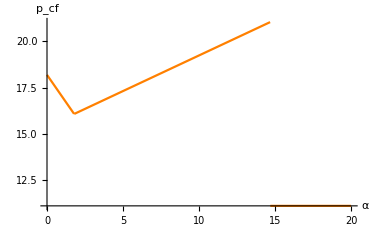

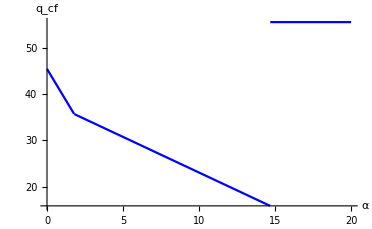

```mathematica
Plot[Piecewise[{{(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))},{(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)},{(2 m γ)/(1+2 γ θ-λ),α≥(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)}}],{α,0,20},PlotStyle->Orange,PlotRange->Automatic,AxesLabel->{α,Subscript[p, cf]}]
Plot[Piecewise[{{(α θ (-2+λ)+m λ)/(4 γ θ-λ^2),α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))},{(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2),(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)},{m/(1+2 γ θ-λ),α≥(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)}}],{α,0,20},PlotStyle->Blue,PlotRange->Automatic,AxesLabel->{α,Subscript[q, cf]}]
```

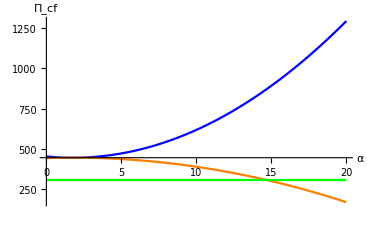

```mathematica
Show[{Plot[Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)],{α,0,20},PlotStyle->Blue],Plot[Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)],{α,0,20},PlotStyle->Orange],Plot[Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)],{α,0,20},PlotStyle->Green]},PlotRange->Automatic,AxesLabel->{α,Subscript[Π, cf]}]
```

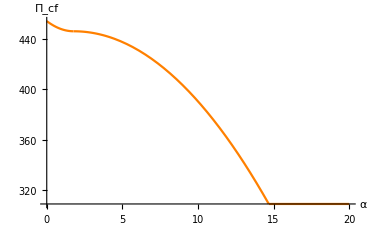

```mathematica
Plot[Piecewise[{{Α[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)],α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))},{Α[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)],(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)},{Π[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)],α≥(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)}}],{α,0,20},PlotStyle->Orange,PlotRange->Automatic,AxesLabel->{α,Subscript[Π, cf]}]
```

## Per-ride Tax

## Basic Model

```mathematica
Clear["Global`*"]
d[p_,q_]:=m-θ*p+λ*q
Π[p_,q_]:=(p-c)*q -γ*q^2
Α[p_,q_]:=(p-c)*d[p,q] -γ*q^2
```

### q <= d

```mathematica
Simplify[D[Π[p,q], q]]
Simplify[D[Π[p,q], p]]
Simplify[D[D[Π[p,q], q],q]]
Simplify[D[D[Π[p,q], p],p]]
Simplify[D[D[Π[p,q], p],q]]
```

-c+p-2 q γ

q

-2 γ

0

1

```mathematica
Simplify[Solve[D[Π[p,q], q]==0,q]]
```

{{q→(-c+p)/(2 γ)}}

```mathematica
Simplify[Π[p,(-c+p)/(2 γ)]]
Simplify[D[Π[p,(-c+p)/(2 γ)],p]]
Simplify[D[D[Π[p,(-c+p)/(2 γ)],p],p]]
Simplify[Solve[D[Π[p,(-c+p)/(2 γ)],p]==0,p]]
```

(c-p)^2/(4 γ)

(-c+p)/(2 γ)

1/(2 γ)

{{p→c}}

```mathematica
Simplify[Solve[d[p,(-c+p)/(2 γ)]==(-c+p)/(2 γ),p]]
Simplify[(-c+(c+2 m γ-c λ)/(1+2 γ θ-λ))/(2 γ)]
```

{{p→(c+2 m γ-c λ)/(1+2 γ θ-λ)}}

(m-c θ)/(1+2 γ θ-λ)

```mathematica
Simplify[Reduce[(c+2 m γ-c λ)/(1+2 γ θ-λ)>c&&m>0&&γ>0&&θ>0&&0<λ<1]]
```

θ>0&&λ>0&&γ>0&&m>0&&λ<1&&c θ<m

```mathematica
Reduce[Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]>0&&m>0&&γ>0&&θ>0&&0<λ<1&&c>0]
```

θ>0&&0<λ<1&&m>0&&((0<c<m/θ&&γ>0)||(c>m/θ&&γ>0))

```mathematica
Simplify[Solve[d[p,q]==q,p]]
Simplify[D[Π[(m+q (-1+λ))/θ,q],q]]
Simplify[D[D[Π[(m+q (-1+λ))/θ,q],q],q]]
```

{{p→(m+q (-1+λ))/θ}}

(m-c θ-2 q (1+γ θ-λ))/θ

-2 γ+(2 (-1+λ))/θ

### q >= d

```mathematica
Simplify[Α[p,q]]
```

-q^2 γ+(-c+p) (m-p θ+q λ)

```mathematica
Simplify[D[Α[p,q], q]]
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], q],q]]
Simplify[D[D[Α[p,q], p],p]]
Simplify[D[D[Α[p,q], p],q]]
```

-2 q γ+(-c+p) λ

m+c θ-2 p θ+q λ

-2 γ

-2 θ

λ

#### Concave

```mathematica
Simplify[Solve[D[Α[p,q], p]==0 && D[Α[p,q], q]==0,{p,q}]]
```

{{p→(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),q→((m-c θ) λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)>c&&0≤d[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]≤((m-c θ) λ)/(4 γ θ-λ^2)&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ]] 
Simplify[Reduce[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)>c&&(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)>0&&0≤d[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]≤((m-c θ) λ)/(4 γ θ-λ^2)&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ]] 
Simplify[Reduce[Α[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0]]
```

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ≤λ&&c θ<m

m>0&&θ>0&&λ>0&&c θ<m&&λ<1&&((λ^2<2 γ θ&&c λ^2<2 γ (m+c θ)&&2 γ θ≤λ)||(λ^2<4 γ θ&&2 γ θ≤λ^2))

θ>0&&0<λ<1&&4 γ θ^2>θ λ^2&&m>0&&c≠m/θ

```mathematica
Simplify[Solve[D[Α[p,q], q]==0,q]]
```

{{q→((-c+p) λ)/(2 γ)}}

```mathematica
Α[p,((-c+p) λ)/(2 γ)]
D[Α[p,((-c+p) λ)/(2 γ)], p]
D[D[Α[p,((-c+p) λ)/(2 γ)], p],p]
```

-((-c+p)^2 λ^2)/(4 γ)+(-c+p) (m-p θ+((-c+p) λ^2)/(2 γ))

m-p θ+(-c+p) (-θ+λ^2/(2 γ))

-2 θ+λ^2/(2 γ)

```mathematica
(* Method 1 *)
Simplify[Solve[d[p,q]==q,q]]
Simplify[Solve[(-m+p θ)/(-1+λ)== ((-c+p) λ)/(2 γ),p]]
Simplify[(-m+((2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)) θ)/(-1+λ)]
(* Method 2 *)
Simplify[Solve[d[p,((-c+p) λ)/(2 γ)]==((-c+p) λ)/(2 γ),p]]
Simplify[((-c+(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)) λ)/(2 γ)]
```

{{q→(-m+p θ)/(-1+λ)}}

{{p→(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)}}

((m-c θ) λ)/(2 γ θ+λ-λ^2)

{{p→(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)}}

((m-c θ) λ)/(2 γ θ+λ-λ^2)

```mathematica
(* Feasibility of boundary point *)
Simplify[Reduce[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)>c&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0]]
Simplify[Reduce[((m-c θ) λ)/(2 γ θ+λ-λ^2)>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0]]
Simplify[Reduce[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)>c&&((m-c θ) λ)/(2 γ θ+λ-λ^2)>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0]]
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0]]
```

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&c θ<m

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&c θ<m

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&c θ<m

θ>0&&0<λ<1&&4 γ θ^2>θ λ^2&&m>0&&c≠m/θ

```mathematica
(* Compare with p1, q1 *)
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&m>0&&c θ<m]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&λ/θ+√(-((-2+λ) λ)/θ^2)>2 γ&&m>0&&c<m/θ

#### Linear

```mathematica
(* 4 γ θ = λ^2, linear in p *)
(* fixed q *)
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], p],p]]
Simplify[Solve[D[Α[p,q], p]==0,p]]
Simplify[D[Α[(m+c θ+q λ)/(2 θ),q],q]]
Simplify[Reduce[0<d[(m+c θ+Q*λ)/(2 θ),Q]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[d[(m+c θ+Q*λ)/(2 θ),Q]>Q&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[0<d[(m+c θ+Q*λ)/(2 θ),Q]≤Q&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[0<d[(m+c θ+Q*λ)/(2 θ),Q]≤Q&&(m+c θ+Q*λ)/(2 θ)>c&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[0<d[(m+c θ+Q*λ)/(2 θ),Q]≤Q&&(m+c θ+Q*λ)/(2 θ)>c&&Α[(m+c θ+Q*λ)/(2 θ),Q]>0&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
```

m+c θ-2 p θ+q λ

-2 θ

{{p→(m+c θ+q λ)/(2 θ)}}

((m-c θ) λ+q (-4 γ θ+λ^2))/(2 θ)

θ>0&&0<λ<1&&Q>0&&m>0&&c<m/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&(m+Q (-2+λ))/θ≤c<m/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&(m+Q (-2+λ))/θ≤c<m/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&(m+Q (-2+λ))/θ≤c<m/θ&&4 γ==λ^2/θ

```mathematica
(* If c<(m+Q (-2+λ))/θ *)
Simplify[Solve[d[p,q]==q&&p==(m+c θ+q λ)/(2 θ),{p,q}]]
Simplify[Reduce[0<d[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]≤(-m+c θ)/(-2+λ)&&(m+c θ-c θ λ)/(2 θ-θ λ)>c&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
```

{{p→(m+c θ-c θ λ)/(2 θ-θ λ),q→(-m+c θ)/(-2+λ)}}

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

```mathematica
(* fixed p *)
Simplify[D[Α[p,q], q]]
Simplify[D[D[Α[p,q],q],q]]
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[D[Α[p,((-c+p) λ)/(2 γ)], p]]
Simplify[Solve[((-c+p) λ)/(2 γ)==Q,p]]
Simplify[Reduce[0<d[c+(2 Q γ)/λ,Q]≤ Q&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[0<d[c+(2 Q γ)/λ,Q]≤ Q&&c+(2 Q γ)/λ>c&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[0<d[c+(2 Q γ)/λ,Q]≤ Q&&c+(2 Q γ)/λ>c&&Α[c+(2 Q γ)/λ,Q]>0&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
```

-2 q γ+(-c+p) λ

-2 γ

{{q→((-c+p) λ)/(2 γ)}}

m-p θ+(-c+p) (-θ+λ^2/(2 γ))

{{p→c+(2 Q γ)/λ}}

θ>0&&0<λ<1&&Q>0&&m>0&&(2 m+Q (-2+λ))/(2 θ)≤c<m/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&(2 m+Q (-2+λ))/(2 θ)≤c<m/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&(2 m+Q (-2+λ))/(2 θ)≤c<m/θ&&4 γ==λ^2/θ

```mathematica
Simplify[Solve[d[p,q]==q&&q==((-c+p) λ)/(2 γ),{p,q}]]
Simplify[Reduce[0<d[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]≤((m-c θ) λ)/(2 γ θ+λ-λ^2)&&(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)>c&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
```

{{p→(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),q→((m-c θ) λ)/(2 γ θ+λ-λ^2)}}

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

```mathematica
(* Compare two boundary *)
Simplify[Reduce[Α[c+(2 Q γ)/λ,Q]<Α[(m+c θ+Q*λ)/(2 θ),Q]&&(m+c θ+Q*λ)/(2 θ)>c&&0<d[(m+c θ+Q*λ)/(2 θ),Q]≤ Q&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[Α[c+(2 Q γ)/λ,Q]>Α[(m+c θ+Q*λ)/(2 θ),Q]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<m/θ]]
Simplify[Reduce[Α[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]>Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
Simplify[Reduce[Α[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]<Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
Simplify[Reduce[Α[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]>0&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
```

θ>0&&0<λ<1&&Q>0&&m>0&&(m+Q (-2+λ))/θ≤c<m/θ&&4 γ==λ^2/θ

False

θ>0&&0<λ<2/3&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

θ>0&&2/3<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

```mathematica
Simplify[Reduce[Α[(m+c θ+Q*λ)/(2 θ),Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&(m+Q (-2+λ))/θ≤c<m/θ]]
Simplify[Reduce[Α[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
Simplify[Reduce[Α[(m+c θ-c θ λ)/(2 θ-θ λ),(-m+c θ)/(-2+λ)]>0&&(m+c θ-c θ λ)/(2 θ-θ λ)>c&&θ>0&&0<λ<1&&4 γ==λ^2/θ&&m>0&&Q>0&&c>m/θ]]
```

4 γ==λ^2/θ&&m>0&&Q>0&&θ>0&&c<m/θ&&((λ==AlgebraicNumber0.793AlgebraicNumber[Root[-4+6 #1-2 #1^2+#1^3&,1],{0,1,0}]0.7932165054721844&&(m+Q (-2+λ))/θ<c)||(0<λ&&λ<AlgebraicNumber0.793AlgebraicNumber[Root[-4+6 #1-2 #1^2+#1^3&,1],{0,1,0}]0.7932165054721844&&(m+Q (-2+λ))/θ≤c)||(λ<1&&(m+(2 Q λ (2-2 λ+λ^2)^2)/(4-8 λ+4 λ^2-4 λ^3+λ^4))/θ<c&&λ>AlgebraicNumber0.793AlgebraicNumber[Root[-4+6 #1-2 #1^2+#1^3&,1],{0,1,0}]0.7932165054721844))

θ>0&&0<λ<Root0.793Root[-4+6 #1-2 #1^2+#1^3&,1]0.7932165054721844&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

θ>0&&0<λ<1&&Q>0&&m>0&&c<(m+Q (-2+λ))/θ&&4 γ==λ^2/θ

False

#### Convex

```mathematica
(* 4 γ θ < λ^2, convex in p *)
(* Fix q *)
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], p],p]]
Simplify[Solve[D[Α[p,q], p]==0,p]]
Simplify[D[Α[(m+c θ+q λ)/(2 θ),q], q]]
Simplify[D[D[Α[(m+c θ+q λ)/(2 θ),q], q],q]]
Simplify[(m+c θ+Q*λ)/(2 θ)]
Simplify[D[D[Α[p,Q],p],p]]
Simplify[Solve[D[Α[p,Q],p]==0,p]]
```

m+c θ-2 p θ+q λ

-2 θ

{{p→(m+c θ+q λ)/(2 θ)}}

((m-c θ) λ+q (-4 γ θ+λ^2))/(2 θ)

-2 γ+λ^2/(2 θ)

(m+c θ+Q λ)/(2 θ)

-2 θ

{{p→(m+c θ+Q λ)/(2 θ)}}

```mathematica
Simplify[Reduce[0<d[(m+c θ+Q λ)/(2 θ),Q]≤Q&&(m+c θ+Q λ)/(2 θ)>c&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
Simplify[Reduce[0<d[(m+c θ+Q λ)/(2 θ),Q]≤Q&&(m+c θ+Q λ)/(2 θ)>c&&Α[(m+c θ+Q λ)/(2 θ),Q]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0,c]]
```

Q>0&&θ>0&&0<γ<λ^2/(4 θ)&&0<λ<1&&((0<c≤(Q λ)/θ&&0<m&&m+Q (-2+λ)≤c θ)||(c>(Q λ)/θ&&c θ<m+Q λ&&c θ≥m+Q (-2+λ)))

m>0&&θ>0&&0<γ<λ^2/(4 θ)&&0<λ<1&&c<(m-2 √((Q^2 γ)/θ) θ+Q λ)/θ&&((Q+m/(-2+λ)≥0&&0<c)||(0<Q&&Q+m/(-2+λ)<0&&(m+Q (-2+λ))/θ≤c))

```mathematica
(* Fix p *)
Simplify[D[Α[p,q], q]]
Simplify[D[D[Α[p,q], q],q]]
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[D[Α[p,((-c+p) λ)/(2 γ)], p]]
Simplify[D[D[Α[p,((-c+p) λ)/(2 γ)], p],p]]
Simplify[Solve[((-c+p) λ)/(2 γ)== Q,p]]
```

-2 q γ+(-c+p) λ

-2 γ

{{q→((-c+p) λ)/(2 γ)}}

m-p θ+(-c+p) (-θ+λ^2/(2 γ))

-2 θ+λ^2/(2 γ)

{{p→c+(2 Q γ)/λ}}

```mathematica
Simplify[Reduce[0<d[c+(2 Q γ)/λ,Q]≤Q&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
Simplify[Reduce[0<d[c+(2 Q γ)/λ,Q]≤Q&&Α[c+(2 Q γ)/λ,Q]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0,c]]
```

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&Q>0&&Q+c θ+(2 Q γ θ)/λ≥m+Q λ&&((c+(2 Q γ)/λ>(Q λ)/θ&&θ (c+(2 Q γ)/λ)<m+Q λ)||(c>0&&m>0&&c+(2 Q γ)/λ≤(Q λ)/θ))

θ>0&&0<λ<1&&0<γ<λ^2/(4 θ)&&m>0&&c+(2 Q γ)/λ<(2 m+Q λ)/(2 θ)&&((Q==(m λ)/(2 γ θ+λ-λ^2)&&(-2 Q γ θ+m λ+Q (-1+λ) λ)/(θ λ)<c)||(Q>(m λ)/(2 γ θ+λ-λ^2)&&0<c)||(0<Q&&Q<(m λ)/(2 γ θ+λ-λ^2)&&(-2 Q γ θ+m λ+Q (-1+λ) λ)/(θ λ)≤c))

```mathematica
(* Boundary *)
Simplify[Solve[d[p,Q]==Q,p]]
Simplify[Reduce[d[p,Q]≤Q&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
```

{{p→(m+Q (-1+λ))/θ}}

c>0&&θ>0&&λ>0&&γ>0&&Q>0&&m>0&&λ<1&&4 γ θ<λ^2&&m+Q λ≤Q+p θ

```mathematica
(* max attainable *)
Simplify[Reduce[(m+c θ+Q λ)/(2 θ)>(m+Q (-1+λ))/θ>c&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
Simplify[Reduce[(m+c θ+Q λ)/(2 θ)>(m+Q (-1+λ))/θ&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
```

θ>0&&λ>0&&Q>0&&c>0&&γ>0&&λ<1&&Q+c θ<m+Q λ&&m+Q (-2+λ)<c θ&&4 γ θ<λ^2

θ>0&&λ>0&&γ>0&&Q>0&&c>0&&m>0&&λ<1&&4 γ θ<λ^2&&m+Q (-2+λ)<c θ

```mathematica
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>Α[(m+c θ+Q λ)/(2 θ),Q]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]]
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ&&c>0&&Q>0]]
```

False

θ>0&&0<λ<1&&m>0&&0<c<m/θ&&(2 (m-c θ) λ^2)/((-2+λ)^2 (2-2 λ+λ^2))<Q<(2 (m-c θ))/(2-2 λ+λ^2)&&4 γ==λ^2/θ

```mathematica
Simplify[d[(m+Q (-1+λ))/θ,Q]-Q]
Simplify[d[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]-(m-c θ)/(1+2 γ θ-λ)]
Simplify[(m+(m-c θ)/(1+2 γ θ-λ) (-1+λ))/θ]
```

0

0

(c+2 m γ-c λ)/(1+2 γ θ-λ)

```mathematica
False
```

```mathematica
Reduce[D[D[Α[(m+q (-1+λ))/θ,q],q],q]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ]
Simplify[Solve[D[Α[(m+q (-1+λ))/θ,q],q]==0,q]]
Simplify[(m-(m+Q (-1+λ))/θ θ)/(2+2 γ θ-2 λ)]
```

False

{{q→(m-c θ)/(2+2 γ θ-2 λ)}}

(Q-Q λ)/(2+2 γ θ-2 λ)

```mathematica
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ&&c>0]]
Simplify[Reduce[d[c+(2 Q γ)/λ,Q]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ&&Q>0&&c>0&&c<m/θ,c]]
```

θ>0&&0<λ<1&&m>0&&(0<c<m/θ||c>m/θ)&&4 γ==λ^2/θ

m>0&&0<λ<1&&Q>0&&θ>0&&4 γ==λ^2/θ&&0<c<m/θ

### Comparing Optimal

```mathematica
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0&&c<(m+Q (-2+λ))/θ]]
(*&&c<(m+Q (-2+λ))/θ*)
(* Simplify[Reduce[Α[(m+c θ+Q λ)/(2 θ),Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ<λ^2/θ&&c>0&&Q>0]] *)
(*&&(m+Q (-2+λ))/θ<c<(m+Q (-1+λ))/θ*)
```

θ>0&&c>0&&m>0&&c<m/θ&&((2 (-1+√2) m>Q+2 (-1+√2) c θ&&(3-2 √2+6 (-1+√2) γ θ+8 γ^2 θ^2) (4 γ θ (-m+c θ)+Q (3-2 √2+6 (-1+√2) γ θ+8 γ^2 θ^2))>0&&√2+2 λ==3&&((θ (-2+√2+4 γ θ)>0&&θ (-11+6 √2+16 γ θ)<0)||(γ>0&&θ>0&&√2+4 γ θ<2)))||((γ θ (-m+c θ)+Q (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)) (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2)>0&&(m-c θ+Q (-2+λ)) (-2+λ)<0&&((4 γ<λ^2/θ&&((γ>0&&√2+2 λ<3&&λ>0)||(λ<AlgebraicNumber0.793AlgebraicNumber[Root[-4+6 #1-2 #1^2+#1^3&,1],{0,1,0}]0.7932165054721844&&√2+2 λ>3&&θ (-1-4 γ θ+2 λ+θ √((-7+12 λ-4 λ^2)/θ^2))<0)))||(λ<1&&√2+2 λ>3&&θ (1+4 γ θ+θ √((-7+12 λ-4 λ^2)/θ^2))<2 θ λ&&γ>0))))

```mathematica
Simplify[Reduce[Α[(m+Q (-1+λ))/θ,Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ&&c>0&&Q>0&&c θ<m&&c<(m+Q (-2+λ))/θ]]
(*&&c<(m+Q (-2+λ))/θ*)
Simplify[Reduce[Α[(m+c θ+Q λ)/(2 θ),Q]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ==λ^2/θ&&c>0&&Q>0&&c θ<m]]
```

θ>0&&0<λ<Root0.793Root[-4+6 #1-2 #1^2+#1^3&,1]0.7932165054721844&&m>0&&0<c<m/θ&&(2 (m-c θ) λ^2)/((-2+λ)^2 (2-2 λ+λ^2))<Q<(-m+c θ)/(-2+λ)&&4 γ==λ^2/θ

4 γ==λ^2/θ&&m>0&&θ>0&&0<c<m/θ&&((Q>0&&0<λ&&√2+λ≤2)||(Q>-((m-c θ) (4-8 λ+4 λ^2-4 λ^3+λ^4))/(2 λ (2-2 λ+λ^2)^2)&&√2+λ>2&&λ<1))

```mathematica
Simplify[Reduce[Α[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ θ≤λ&&m>0&&c θ<m]]
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ θ>λ&&m>0&&c θ<m&&c>0]]
Simplify[Reduce[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]<Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ θ>λ&&m>0&&c θ<m&&c>0]]
```

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ≤λ&&c θ<m

θ>0&&0<λ<1&&2 γ>λ/θ&&λ/θ+√(-((-2+λ) λ)/θ^2)>2 γ&&m>0&&0<c<m/θ

θ>0&&0<λ<1&&θ (-2 γ θ+λ+θ √(-((-2+λ) λ)/θ^2))<0&&m>0&&0<c<m/θ

## Comparative Stats

```mathematica
D[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c]
D[((m-c θ) λ)/(4 γ θ-λ^2),c]
```

(2 γ θ-λ^2)/(4 γ θ-λ^2)

-(θ λ)/(4 γ θ-λ^2)

```mathematica
Reduce[D[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c]≥0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2<4 γ θ&&2 γ θ≤λ&&c θ<m]
Reduce[D[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c]≤0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2<4 γ θ&&2 γ θ≤λ&&c θ<m]
Reduce[D[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c]≥0&&0<γ&&θ>0&&m>0&&0<λ<1&&c θ<m]
Reduce[D[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c]≤0&&0<γ&&θ>0&&m>0&&0<λ<1&&c θ<m]
Reduce[D[((m-c θ) λ)/(4 γ θ-λ^2),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2<4 γ θ&&2 γ θ≤λ&&c θ<m]
```

θ>0&&0<λ<1&&λ^2/(2 θ)≤γ≤λ/(2 θ)&&m>0&&c<m/θ

θ>0&&0<λ<1&&λ^2/(4 θ)<γ≤λ^2/(2 θ)&&m>0&&c<m/θ

θ>0&&0<λ<1&&((0<γ<λ^2/(4 θ)&&m>0&&c<m/θ)||(γ≥λ^2/(2 θ)&&m>0&&c<m/θ))

θ>0&&0<λ<1&&λ^2/(4 θ)<γ≤λ^2/(2 θ)&&m>0&&c<m/θ

False

```mathematica
D[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),c]
D[((m-c θ) λ)/(2 γ θ+λ-λ^2),c]
```

-((-1+λ) λ)/(2 γ θ+λ-λ^2)

-(θ λ)/(2 γ θ+λ-λ^2)

```mathematica
Reduce[D[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≤4 γ θ&&c θ<m]
Reduce[D[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),c]<0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≤4 γ θ&&c θ<m]
Reduce[D[((m-c θ) λ)/(2 γ θ+λ-λ^2),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≤4 γ θ&&c θ<m]
```

θ>0&&0<λ<1&&γ≥λ^2/(4 θ)&&m>0&&c<m/θ

False

False

```mathematica
D[(c+2 m γ-c λ)/(1+2 γ θ-λ),c]
D[(m-c θ)/(1+2 γ θ-λ),c]
```

(1-λ)/(1+2 γ θ-λ)

-θ/(1+2 γ θ-λ)

```mathematica
Reduce[D[(c+2 m γ-c λ)/(1+2 γ θ-λ),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≤4 γ θ&&c θ<m]
Reduce[D[(m-c θ)/(1+2 γ θ-λ),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≤4 γ θ&&c θ<m]
```

θ>0&&0<λ<1&&γ≥λ^2/(4 θ)&&m>0&&c<m/θ

False

```mathematica
D[(m+Q (-1+λ))/θ,c]
D[(m+c θ+Q λ)/(2 θ),c]
```

0

1/2

```mathematica
Reduce[D[(m+Q (-1+λ))/θ,c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≥4 γ θ&&c θ≥m]
Reduce[D[(m+c θ+Q λ)/(2 θ),c]>0&&0<γ&&θ>0&&m>0&&0<λ<1&&λ^2≥4 γ θ&&c θ≥m]
```

False

θ>0&&0<λ<1&&0<γ≤λ^2/(4 θ)&&m>0&&c≥m/θ

## Plot

```mathematica
Α[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]
Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)]
Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]
```

-(γ (m-c θ)^2 λ^2)/((4 γ θ-λ^2)^2)+(-c+(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)) (m+((m-c θ) λ^2)/(4 γ θ-λ^2)-(θ (2 m γ+2 c γ θ-c λ^2))/(4 γ θ-λ^2))

-(γ (m-c θ)^2 λ^2)/((2 γ θ+λ-λ^2)^2)+(-c+(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2)) (m+((m-c θ) λ^2)/(2 γ θ+λ-λ^2)-(θ (2 m γ-c (-1+λ) λ))/(2 γ θ+λ-λ^2))

-(γ (m-c θ)^2)/(1+2 γ θ-λ)^2+((m-c θ) (-c+(c+2 m γ-c λ)/(1+2 γ θ-λ)))/(1+2 γ θ-λ)

### 4 γ>λ^2/θ&&γ<λ/(2 θ)

```mathematica
m = 50;λ = 0.5; θ = 2; γ = 0.1;
m/θ
```

25

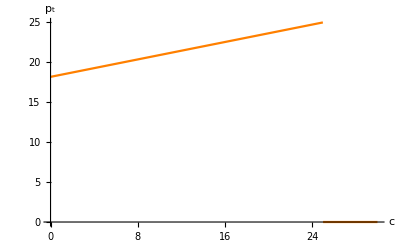

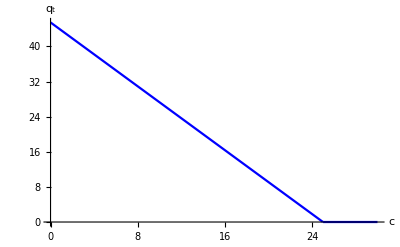

```mathematica
Plot[Piecewise[{{(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),c<m/θ},{0,c≥m/θ}}],{c,0,30},PlotStyle->Orange,PlotRange->All,AxesLabel->{c,Subscript[p, t]}]
Plot[Piecewise[{{((m-c θ) λ)/(4 γ θ-λ^2),c<m/θ},{0,c≥m/θ}}],{c,0,30},PlotStyle->Blue,PlotRange->All,AxesLabel->{c,Subscript[q, t]}]
```

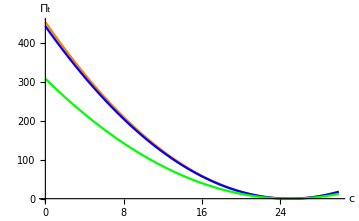

```mathematica
Show[{Plot[Α[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)],{c,0,30},PlotStyle->Orange],Plot[Α[(2 m γ-c (-1+λ) λ)/(2 γ θ+λ-λ^2),((m-c θ) λ)/(2 γ θ+λ-λ^2)],{c,0,30},PlotStyle->Blue],Plot[Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)],{c,0,30},PlotStyle->Green]},PlotRange->All,AxesLabel->{c,Subscript[Π, t]}]
```

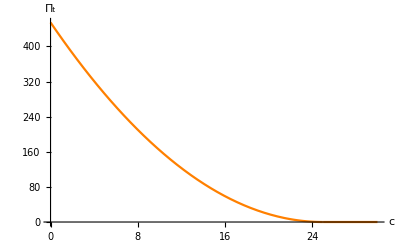

```mathematica
Plot[Piecewise[{{Α[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)],c<m/θ},{0,c≥m/θ}}],{c,0,30},PlotStyle->Orange,PlotRange->All,AxesLabel->{c,Subscript[Π, t]}]
```

## Equivalence

```mathematica
Simplify[Solve[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)==(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)&&(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)==((m-c θ) λ)/(4 γ θ-λ^2)]]
```

{{c→0,α→0},{c→α (-1+1/λ),θ→0}}

```mathematica
(* B2 *)
Simplify[Solve[-(m+α θ (-1+λ))/(θ (-2+λ))==(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)&&(m+α θ)/(2-λ)==((m-c θ) λ)/(4 γ θ-λ^2)]]
(* B1 *)
Simplify[Solve[(2 m γ)/(1+2 γ θ-λ)==(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)&&m/(1+2 γ θ-λ)==((m-c θ) λ)/(4 γ θ-λ^2)]]
```

{{c→-α,m→-α θ},{c→-α,γ→λ/(2 θ)}}

{{c→0,m→0},{m→(c λ)/(2 γ (-1+λ)),θ→λ/(2 γ)},{c→0,m→0,θ→1/(2 γ)},{c→0,θ→1/(2 γ),λ→1}}

## Compare Two Policies

```mathematica
Clear["Global`*"]
d[p_,q_]:=m-θ*p+λ*q
SW[p_,q_]:=p*d[p,q]-γ*q^2+d[p,q]-β*q
```

## Congestion Fee

```mathematica
Simplify[SW[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]]
Simplify[SW[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]]
Simplify[SW[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]]
```

(m^2 γ+m (2 γ θ-β λ)-α θ (α-2 β-2 γ θ+α γ θ+λ-α λ+β λ))/(4 γ θ-λ^2)

-((α θ (-1+λ)+m λ) (m γ (-2+λ)+α (1+γ θ-λ) (-1+λ)+(-1+β) (2 γ θ+λ-λ^2)))/((2 γ θ+λ-λ^2)^2)

(m (1+m γ+2 γ θ-λ+β (-1-2 γ θ+λ)))/(-1-2 γ θ+λ)^2

## Per-ride Tax

```mathematica
Simplify[SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]]
```

((m-c θ) (m γ+(2+c) γ θ-β λ))/(4 γ θ-λ^2)

## Compare

### Case I

```mathematica
Simplify[Reduce[SW[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]≥SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&c<m/θ&&α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
```

β∈ℝ&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&((c<α (-1+2/λ)&&β≥(c (2+c) γ θ+α (2 γ θ-λ)+α^2 (-1-γ θ+λ))/(α (-2+λ)+c λ))||c+α==(2 α)/λ||(c+α>(2 α)/λ&&c<m/θ&&β≤(c (2+c) γ θ+α (2 γ θ-λ)+α^2 (-1-γ θ+λ))/(α (-2+λ)+c λ)))

```mathematica
Simplify[SW[(2 m γ+2 *α *(-1+2/λ)* γ θ-α *(-1+2/λ)* λ^2)/(4 γ θ-λ^2),((m-α *(-1+2/λ)* θ) λ)/(4 γ θ-λ^2)]]

Simplify[SW[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]-SW[(2 m γ+2 *α *(-1+2/λ)* γ θ-α *(-1+2/λ)* λ^2)/(4 γ θ-λ^2),((m-α *(-1+2/λ)* θ) λ)/(4 γ θ-λ^2)]]
```

((α θ (-2+λ)+m λ) (α γ θ (-2+λ)+λ (-m γ-2 γ θ+β λ)))/(-4 γ θ λ^2+λ^4)

(α θ (α+λ-α λ))/λ^2

```mathematica
Simplify[Solve[c+α==(2 α)/λ,α]]
Simplify[-(m/θ* λ)/(-2+λ)]
```

{{α→-(c λ)/(-2+λ)}}

(m λ)/(2 θ-θ λ)

```mathematica
Simplify[Reduce[(m λ)/(2 θ-θ λ)<(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
```

False

```mathematica
Simplify[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))* (-1+2/λ)]
Simplify[Reduce[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))* (-1+2/λ)<m/θ&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
```

(m (-1+2/λ) (-2 γ θ+λ))/(2 θ (1+γ θ-λ))

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

### Case II

```mathematica
Simplify[Reduce[SW[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]≥SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&c<m/θ&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)]]
```

β∈ℝ&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))&&((c<(m λ (-2 γ θ+λ)+α θ (-1+λ) (-4 γ θ+λ^2))/(θ λ (2 γ θ+λ-λ^2))&&β≥(-m^2 γ (-2 γ θ+λ)^2+c (2+c) γ θ^2 (2 γ θ+λ-λ^2)^2+α (-1+λ) (-4 γ θ+λ^2) (m (2 γ θ-λ) (-1+λ)+θ (-2 γ θ+(-1+λ) λ))+m (-8 γ^3 θ^3+8 γ^2 θ^2 λ^2+(-1+λ) λ^4-2 γ θ λ^2 (-1+λ+λ^2))-α^2 θ (-1+λ)^2 (4 γ^2 θ^2+(-1+λ) λ^2-γ θ (-4+4 λ+λ^2)))/((2 γ θ+λ-λ^2) (m (2 γ θ-λ) λ+α θ (-1+λ) (4 γ θ-λ^2)+c θ λ (2 γ θ+λ-λ^2))))||c==(m λ (-2 γ θ+λ)+α θ (-1+λ) (-4 γ θ+λ^2))/(θ λ (2 γ θ+λ-λ^2))||((m λ (-2 γ θ+λ)+α θ (-1+λ) (-4 γ θ+λ^2))/(θ λ (2 γ θ+λ-λ^2))<c<m/θ&&β≤(-m^2 γ (-2 γ θ+λ)^2+c (2+c) γ θ^2 (2 γ θ+λ-λ^2)^2+α (-1+λ) (-4 γ θ+λ^2) (m (2 γ θ-λ) (-1+λ)+θ (-2 γ θ+(-1+λ) λ))+m (-8 γ^3 θ^3+8 γ^2 θ^2 λ^2+(-1+λ) λ^4-2 γ θ λ^2 (-1+λ+λ^2))-α^2 θ (-1+λ)^2 (4 γ^2 θ^2+(-1+λ) λ^2-γ θ (-4+4 λ+λ^2)))/((2 γ θ+λ-λ^2) (m (2 γ θ-λ) λ+α θ (-1+λ) (4 γ θ-λ^2)+c θ λ (2 γ θ+λ-λ^2)))))

```mathematica
Solve[c==(m λ (-2 γ θ+λ)+α θ (-1+λ) (-4 γ θ+λ^2))/(θ λ (2 γ θ+λ-λ^2)),α]
```

{{α→(λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))}}

```mathematica
Simplify[Reduce[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<(λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&(m (-1+2/λ) (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<c<m/θ]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(m (2 γ θ-λ) (-2+λ))/(2 θ (1+γ θ-λ) λ)<c<(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)

```mathematica
Simplify[SW[((λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))+2 m γ-2 ((λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))) λ+((λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))) λ^2)/(2 γ θ+λ-λ^2),(((λ (-2 m γ θ-2 c γ θ^2+m λ-c θ λ+c θ λ^2))/(θ (-1+λ) (4 γ θ-λ^2))) θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]-SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]]
```

((-m+c θ) (2 γ θ-λ) (m (2 γ θ-λ)+θ (2 (2+c) γ θ-λ (c (-1+λ)+λ))))/(θ (-4 γ θ+λ^2)^2)

### Case III

```mathematica
Simplify[Reduce[SW[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]≥SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ&&α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α≤(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ&&β≤(c (2+c) γ θ+α (2 γ θ-λ)+α^2 (-1-γ θ+λ))/(α (-2+λ)+c λ)

```mathematica
Simplify[Reduce[SW[(α+2 m γ-2 α λ+α λ^2)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+m λ)/(2 γ θ+λ-λ^2)]≥SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(-2 m γ^2 θ^2+m λ+2 m γ θ λ-m λ^2)/(θ+3 γ θ^2+2 γ^2 θ^3-2 θ λ-3 γ θ^2 λ+θ λ^2)]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<α<(m (-2 γ^2 θ^2+λ+2 γ θ λ-λ^2))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ&&β≤(-m^2 γ (-2 γ θ+λ)^2+c (2+c) γ θ^2 (2 γ θ+λ-λ^2)^2+α (-1+λ) (-4 γ θ+λ^2) (m (2 γ θ-λ) (-1+λ)+θ (-2 γ θ+(-1+λ) λ))+m (-8 γ^3 θ^3+8 γ^2 θ^2 λ^2+(-1+λ) λ^4-2 γ θ λ^2 (-1+λ+λ^2))-α^2 θ (-1+λ)^2 (4 γ^2 θ^2+(-1+λ) λ^2-γ θ (-4+4 λ+λ^2)))/((2 γ θ+λ-λ^2) (m (2 γ θ-λ) λ+α θ (-1+λ) (4 γ θ-λ^2)+c θ λ (2 γ θ+λ-λ^2)))

```mathematica
Simplify[Reduce[SW[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]≥SW[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ]]
```

α>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&(m (2 γ^2 θ^2 (-2+λ)+γ θ (3-2 λ) λ+(-1+λ)^2 λ))/(θ (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ)<c<m/θ&&β≤(c (2+c) γ θ^2 (-1-2 γ θ+λ)^2-m^2 γ (1+4 γ^2 θ^2-2 λ-4 γ θ λ+2 λ^2)+m (-8 γ^3 θ^3+8 γ^2 θ^2 λ+(-1+λ) λ^2+γ θ (2-4 λ^2)))/((1+2 γ θ-λ) (c θ (1+2 γ θ-λ) λ-m (2 γ θ (-2+λ)+λ)))

## Social Welfare

## Basic Model

```mathematica
Clear["Global`*"]
d[p_,q_]:=m-θ*p+λ*q
SW1[p_,q_]:=p*q-γ*q^2+d[p,q]-β*q
SW2[p_,q_]:=p*d[p,q]-γ*q^2+d[p,q]-β*q
Simplify[SW1[p,q]]
Simplify[SW2[p,q]]
```

m+p (q-θ)-q (β+q γ-λ)

m (1+p)-q^2 γ-p (1+p) θ+q (-β+λ+p λ)

### q <= d

```mathematica
Simplify[D[SW1[p,q], q]]
Simplify[D[SW1[p,q], p]]
Simplify[D[D[SW1[p,q], q],q]]
Simplify[D[D[SW1[p,q], p],p]]
Simplify[D[D[SW1[p,q], p],q]]
```

p-β-2 q γ+λ

q-θ

-2 γ

0

1

```mathematica
(* Fix p *)
Simplify[Solve[D[SW1[p,q], q]==0,q]]
Simplify[D[SW1[p,(p-β+λ)/(2 γ)],p]]
Simplify[D[D[SW1[p,(p-β+λ)/(2 γ)],p],p]]
Simplify[Solve[D[SW1[p,(p-β+λ)/(2 γ)],p]==0,p]]
Simplify[Reduce[d[p,q]≥q&&0<γ&&θ>0&&0<λ<1&&β>0,p]]
```

{{q→(p-β+λ)/(2 γ)}}

(p-β-2 γ θ+λ)/(2 γ)

1/(2 γ)

{{p→β+2 γ θ-λ}}

(m|q)∈ℝ&&γ>0&&θ>0&&0<λ<1&&β>0&&p≤(m+q (-1+λ))/θ

```mathematica
(* method 1 *)
Simplify[Reduce[d[p,(p-β+λ)/(2 γ)]≥(p-β+λ)/(2 γ)&&0<γ&&θ>0&&0<λ<1&&β>0,p]]
(* method 2, best response & boundary *)
Simplify[Solve[p==(m+q (-1+λ))/θ&&q==(p-β+λ)/(2 γ),{p,q}]]
```

m∈ℝ&&θ>0&&0<λ<1&&γ>0&&β>0&&p≤(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)

{{p→(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),q→(m-β θ+θ λ)/(1+2 γ θ-λ)}}

```mathematica
(* Feasibility *)
Simplify[Reduce[β+2 γ θ-λ≥1/2*(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
Simplify[Reduce[β+2 γ θ-λ≥1/2*(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>λ&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
Simplify[Reduce[β+2 γ θ-λ≥1/2*(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)&&0<γ&&θ>0&&0<λ<1&&m>0&&β<λ&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&0<m<2 θ (1+2 γ θ-λ)&&(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)≤β<λ

```mathematica
(* Compare directly *)
(* Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]>SW1[0,(-β+λ)/(2 γ)]&&(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)≥0&&(m-β θ+θ λ)/(1+2 γ θ-λ)≥0&&(-β+λ)/(2 γ)≥0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0,β]] *)
```

```mathematica
Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)>0&&(m-β θ+θ λ)/(1+2 γ θ-λ)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]>0&&SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]>SW1[0,(-β+λ)/(2 γ)]&&(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)>0&&(m-β θ+θ λ)/(1+2 γ θ-λ)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0,β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&((0<β≤λ&&m>0)||(β+λ>2+(-1+λ)^2/(γ θ)&&((0<m&&m+(-1+λ)^2/γ<θ (-2+β+λ))||m+θ λ>β θ))||(λ<β&&m+θ λ>β θ))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&((0<β≤λ&&m>((β-λ) (-1+λ))/(2 γ))||(β>λ&&m+θ λ>β θ))

γ>0&&0<λ<1&&0<θ&&β<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)&&((θ+m/(-1+λ)<0&&((2 m+((-1+λ) λ)/γ==0&&0<β)||(0<m&&(2 m γ)/(-1+λ)+λ<β&&γ (2 m γ+(-1+λ) λ)<0)))||(γ (2 m γ+(-1+λ) λ)>0&&0<β&&γ (-1+2 λ+γ (-4 θ+√((1+4 m γ-2 λ+2 λ^2)/γ^2)))>0))

```mathematica
Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0]]
```

θ>0&&β>0&&0<λ<1&&γ>0&&m>0

### q >= d

```mathematica
Simplify[D[SW2[p,q], q]]
Simplify[D[SW2[p,q], p]]
Simplify[D[D[SW2[p,q], q],q]]
Simplify[D[D[SW2[p,q], p],p]]
Simplify[D[D[SW2[p,q], p],q]]
```

-β-2 q γ+λ+p λ

m-(1+2 p) θ+q λ

-2 γ

-2 θ

λ

```mathematica
Simplify[Solve[D[SW2[p,q], p]==0 && D[SW2[p,q], q]==0,{p,q}]]
```

{{p→(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),q→(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[d[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]≤(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)&&(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)>0&&(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
Simplify[Reduce[SW2[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
```

θ>0&&((m>0&&β>0&&θ>0&&m<θ&&λ^2<4 γ θ&&((θ<m+θ λ&&2 γ θ<λ&&λ<1&&λ<2&&2 θ (β+γ (m+θ))≤(m+θ+β θ) λ)||(λ>0&&2 γ θ+β λ<2 m γ+λ^2&&m+θ λ≤θ)))||(m≥θ&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&0<β≤((m+θ) (2 γ θ-λ))/(θ (-2+λ))))

θ>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β&&λ<1&&((m/θ+λ>1&&0<m&&β<(2 m γ-2 γ θ+λ^2)/λ&&m≤θ)||(m>θ&&λ>0&&λ+(m λ)/θ>2 β))

θ>0&&λ>0&&m>0&&β>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

```mathematica
Simplify[Solve[D[SW2[p,q], q]==0,q]]
Reduce[d[p, (-β+λ+p λ)/(2 γ)]≤(-β+λ+p λ)/(2 γ)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ,p]
Simplify[(-β+λ+((β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)) λ)/(2 γ)]
(* Sanity check *)
Simplify[Reduce[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)≥(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))]]
```

{{q→(-β+λ+p λ)/(2 γ)}}

θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&β>0&&m>0&&p≥(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)

(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)

False

```mathematica
(* Feasibility of boundary solution *)
Simplify[Reduce[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&& (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ)),β]]
Simplify[Reduce[SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ)),β]]
Simplify[Reduce[SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]>0&&(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&& (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ)),β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β<((m+θ) λ)/θ&&((m+θ λ>θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β)||(m>0&&(2 m γ)/(-1+λ)+λ<β&&m+θ λ≤θ))

m>0&&θ>0&&((((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<((m+θ) λ)/θ&&((4 γ>λ^2/θ&&2 γ<λ/θ&&(0<λ≤1/2||2/3≤λ<1))||(1/2<λ<2/3&&(λ^2/(4 θ)<γ≤(-1+λ)^2/θ||(-1+λ)^2/θ<γ<λ/(2 θ)))))||(β>-(γ (m+θ) (-2+λ))/(γ θ-(-1+λ)^2)&&((1/2<λ<2/3&&(-1+λ)^2/θ<γ<λ/(2 θ))||(2/3≤λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ))))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β<((m+θ) λ)/θ&&((m+θ λ>θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β)||(m>0&&(2 m γ)/(-1+λ)+λ<β&&m+θ λ≤θ))

```mathematica
Simplify[Reduce[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ)),β]]
Simplify[Reduce[(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ)),β]]
Reduce[(2 m γ)/(-1+λ)+λ>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&m+θ λ≤θ]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&((m>0&&m+θ λ≤θ&&β>(2 m γ)/(-1+λ)+λ)||(m+θ λ>θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))))

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

θ>0&&0<λ<1&&γ>0&&0<m<θ-θ λ

### Compare Optimal

```mathematica
(* Compare beta *)
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))≥(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)<m/θ+ λ&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)<(2 m γ)/(-1+λ)+λ&&m/θ+ λ<1&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)> λ&&m/θ+ λ>1&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

β>0&&θ>0&&0<λ<1&&((m>0&&(γ==(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)||((-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)<γ≤(-1+2 λ+θ √((1-2 λ+2 λ^2)/θ^2))/(4 θ)&&m+θ λ≤θ)))||(λ^2/(4 θ)<γ<(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)&&m+θ λ≥θ)||(2 γ<λ/θ&&1/2 (8 γ θ^2+θ (4-8 λ)+((-1+λ) λ)/γ)<m&&θ (-1-4 γ θ+2 λ+θ √((1-2 λ+2 λ^2)/θ^2))<0&&m+θ λ≤θ))

β>0&&θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

β>0&&θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&m+θ λ<θ

β>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&2 θ (1+2 γ θ-λ)<m

```mathematica
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))≥(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&m/θ+ λ>1]]
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))≥(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&m/θ+ λ<1]]
```

β>0&&θ>0&&0<λ<1&&λ^2/(4 θ)<γ≤(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)&&m+θ λ>θ

β>0&&θ>0&&0<λ<1&&m+θ λ<θ&&((m>0&&(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)≤γ≤(-1+2 λ+θ √((1-2 λ+2 λ^2)/θ^2))/(4 θ))||(2 γ<λ/θ&&1/2 (8 γ θ^2+θ (4-8 λ)+((-1+λ) λ)/γ)<m&&θ (-1-4 γ θ+2 λ+θ √((1-2 λ+2 λ^2)/θ^2))<0))

```mathematica
(* Compare boundary soln *)
(* Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)]]*)
Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<((m+θ) λ)/θ&&β<λ]]
Simplify[Reduce[SW1[β-λ,0]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<((m+θ) λ)/θ&&β>λ]]
```

θ>0&&0<λ<1&&((4 γ>λ^2/θ&&λ^2/θ+√(-((-2+λ) λ^3)/θ^2)≥4 γ&&(((2 γ θ-λ)/(-2+λ)<β&&β+2 γ θ≤λ&&0<m&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ))||(-2 γ θ+λ<β<λ&&(0<m<((β-λ) (-1+λ))/(2 γ)||(4 β γ θ+8 γ^2 θ^2+β λ^2-4 γ θ λ^2-λ^3-β λ^3+λ^4)/(4 γ λ-2 γ λ^2)<m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)))))||(λ^2/θ+√(-((-2+λ) λ^3)/θ^2)<4 γ&&2 γ<λ/θ&&(((2 γ θ-λ)/(-2+λ)<β&&β+2 γ θ<λ&&0<m&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ))||(β+2 γ θ==λ&&0<m<(4 β γ θ+8 γ^2 θ^2+β λ^2-4 γ θ λ^2-λ^3-β λ^3+λ^4)/(4 γ λ-2 γ λ^2))||(-2 γ θ+λ<β<λ&&(0<m<((β-λ) (-1+λ))/(2 γ)||(4 β γ θ+8 γ^2 θ^2+β λ^2-4 γ θ λ^2-λ^3-β λ^3+λ^4)/(4 γ λ-2 γ λ^2)<m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ))))))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>λ&&-1/(2 γ (-2+λ) λ)(2 β γ θ+4 γ^2 θ^2-β λ+λ^2+2 β λ^2-2 γ θ λ^2-2 λ^3-β λ^3+λ^4+2 γ λ √(((2 γ θ+λ-λ^2)^2 (4 γ^2 θ^2+β^2 (-1+λ)^2+2 β (2 γ θ-λ) (-1+λ)^2-4 γ θ (-1+λ)^2 λ+(-1+λ)^2 λ^2))/(γ^2 (-2+λ)^2 λ^2))-γ λ^2 √(((2 γ θ+λ-λ^2)^2 (4 γ^2 θ^2+β^2 (-1+λ)^2+2 β (2 γ θ-λ) (-1+λ)^2-4 γ θ (-1+λ)^2 λ+(-1+λ)^2 λ^2))/(γ^2 (-2+λ)^2 λ^2)))<m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)

```mathematica
Simplify[Solve[d[p,q]==q,p]]
```

{{p→(m+q (-1+λ))/θ}}

```mathematica
Simplify[SW1[(m+q (-1+λ))/θ,q]-SW2[(m+q (-1+λ))/θ,q]]
(* Concave in q *)
Simplify[D[D[SW1[(m+q (-1+λ))/θ,q],q],q]]
Simplify[D[D[SW2[(m+q (-1+λ))/θ,q],q],q]]
```

0

-2 γ+(2 (-1+λ))/θ

-2 γ+(2 (-1+λ))/θ

```mathematica
Simplify[Solve[D[SW2[(m+q (-1+λ))/θ,q],q]==0,q]]
```

{{q→(m+θ-β θ)/(2+2 γ θ-2 λ)}}

### Compare Optimal for different cases

#### Case I

```mathematica
Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&&(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<m/θ+ λ&&m/θ+ λ>1&&β<λ]]
Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<m/θ+ λ&&m/θ+ λ>1&&β>λ]]
(* Simplify[Reduce[SW1[β-λ,0]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<m/θ+ λ&&m/θ+ λ>1&&β>λ]]*)
Simplify[Reduce[SW1[β-λ,0]<SW1[0,(-β+λ)/(2 γ)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<m/θ+ λ&&m/θ+ λ>1&&β>λ]]
```

θ>0&&0<λ&&λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&λ<β+2 γ θ&&β<λ&&γ (-2+λ) λ (8 γ^2 θ^2+(-1+λ) λ^3+2 γ λ (m (-2+λ)-2 θ λ)+β (4 γ θ+λ^2-λ^3))>0&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>λ&&(4 β γ θ+8 γ^2 θ^2+β λ^2-4 γ θ λ^2-λ^3-β λ^3+λ^4)/(4 γ λ-2 γ λ^2)<m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)

θ>0&&((λ<1&&2 γ<λ/θ&&4 γ>λ^2/θ&&((m>θ&&λ>0&&m/θ+λ>β&&λ+(m λ)/θ≤2 β)||(m>0&&m≤θ&&β>λ&&m+θ λ>θ&&m+θ λ>β θ)))||(m>θ&&1/2 ((β (-2+λ))/(m+θ)+λ/θ)<γ<λ/(2 θ)&&λ<β<((m+θ) λ)/(2 θ)&&0<λ<1))

#### Case II

```mathematica
Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)&&β<m/θ+ λ&&m/θ+ λ>1]]
Simplify[Reduce[SW1[(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ),(m-β θ+θ λ)/(1+2 γ θ-λ)]>SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)&&β<m/θ+ λ&&m/θ+ λ>1]]
(*Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&(β+2 m γ-β λ+(-1+λ) λ)/(1+2 γ θ-λ)>0&&(m-β θ+θ λ)/(1+2 γ θ-λ)>0&&(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&&(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<m/θ+ λ&&m/θ+ λ>1]]*)
```

θ>0&&0<λ<1&&(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)<γ<λ/(2 θ)&&m+θ λ>θ&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)

False

```mathematica
(* Compare beta *)
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)&&(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)<(2 γ^2 θ^2 (m+2 θ)+(-1+λ) λ (m+θ λ)-γ θ (2 m λ+θ (-2+3 λ+λ^2)))/(θ (-1+γ θ (-3+λ)+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&m/θ+ λ>1]]
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))<(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)&&(2 m γ-4 γ θ-8 γ^2 θ^2+λ+8 γ θ λ-λ^2)/(1+4 γ θ-λ)<(-8 γ^2 θ^2-(-1+λ) λ^3+2 γ λ (-m (-2+λ)+2 θ λ))/(4 γ θ+λ^2-λ^3)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&m/θ+ λ>1]]
```

β>0&&θ>0&&0<λ<1&&(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)<γ<λ/(2 θ)&&m+θ λ>θ

β>0&&θ>0&&0<λ<1&&(-3+4 λ+θ √((9-16 λ+8 λ^2)/θ^2))/(8 θ)<γ<λ/(2 θ)&&m+θ λ>θ

#### Case III

```mathematica
Simplify[Reduce[SW1[0,(-β+λ)/(2 γ)]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&&(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>(2 m γ)/(-1+λ)+λ&&β<m/θ+ λ&&m/θ+ λ<1]]
Simplify[Reduce[SW1[β-λ,0]<SW2[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]&&(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)>0&&(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)>0&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&β>(2 m γ)/(-1+λ)+λ&&β<m/θ+ λ&&m/θ+ λ<1]]
```

False

False

### Quadratic consumer welfare

```mathematica
(* Quadratic consumer welfare *)
SW3[p_,q_]:=p*q-γ*q^2+(d[p,q])^2-β*q
SW4[p_,q_]:=p*d[p,q]-γ*q^2+(d[p,q])^2-β*q
```

#### q <= d

```mathematica
Simplify[D[SW3[p,q], q]]
Simplify[D[SW3[p,q], p]]
Simplify[D[D[SW3[p,q], q],q]]
Simplify[D[D[SW3[p,q], p],p]]
Simplify[D[D[SW3[p,q], p],q]]
```

p-β-2 q γ+2 λ (m-p θ+q λ)

q-2 θ (m-p θ+q λ)

-2 γ+2 λ^2

2 θ^2

1-2 θ λ

```mathematica
(* Hessian *)
Simplify[(-2 γ+2 λ^2)*2 θ^2-(1-2 θ λ)^2]
```

-1-4 γ θ^2+4 θ λ

```mathematica
Simplify[Reduce[-1-4 γ θ^2+4 θ λ>0&&-2 γ+2 λ^2<0&&2 θ^2<0&&0<γ&&θ>0&&0<λ<1]]
```

False

#### q >= d

```mathematica
Simplify[D[SW4[p,q], q]]
Simplify[D[SW4[p,q], p]]
Simplify[D[D[SW4[p,q], q],q]]
Simplify[D[D[SW4[p,q], p],p]]
Simplify[D[D[SW4[p,q], p],q]]
```

-β-2 q γ+p λ+2 λ (m-p θ+q λ)

m-2 m θ+2 p (-1+θ) θ+q (1-2 θ) λ

-2 γ+2 λ^2

2 (-1+θ) θ

λ-2 θ λ

```mathematica
(* Hessian *)
Simplify[(-2 γ+2 λ^2)*(2 (-1+θ) θ)-(λ-2 θ λ)^2]
```

-4 γ (-1+θ) θ-λ^2

```mathematica
Simplify[Reduce[-4 γ (-1+θ) θ-λ^2>0&&-2 γ+2 λ^2<0&&2 (-1+θ) θ<0&&0<γ&&θ>0&&0<λ<1]]
Simplify[Reduce[-4 γ (-1+θ) θ-λ^2>0&&-2 γ+2 λ^2<0&&2 (-1+θ) θ<0&&0<γ&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

λ>0&&θ>0&&λ<1&&θ<1&&4 γ (-1+θ) θ+λ^2<0

λ>0&&θ>0&&λ<1&&2 θ+λ<2&&θ<1&&4 γ (-1+θ) θ+λ^2<0&&2 γ θ<λ

```mathematica
Simplify[Solve[D[SW4[p,q], p]==0 && D[SW4[p,q], q]==0,{p,q}]]
```

{{p→((-1+2 θ) (2 m γ-β λ))/(4 γ (-1+θ) θ+λ^2),q→-(2 β (-1+θ) θ+m λ)/(4 γ (-1+θ) θ+λ^2)}}

## Coordination

```mathematica
(* Interior soln *)
[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]
(* Boundary soln *)
[(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2), (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]
[β-λ,0]
```

### Congestion Fee

```mathematica
(* Interior soln *)
[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2),(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)]
(* Boundary 2 *)
[-(m+α θ (-1+λ))/(θ (-2+λ)), (m+α θ)/(2-λ)]
(* Boundary 1 *)
[(2 m γ)/(1+2 γ θ-λ),m/(1+2 γ θ-λ)]
```

#### β < β bar

```mathematica
Simplify[Solve[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&&(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]]
Simplify[Solve[-(m+α θ (-1+λ))/(θ (-2+λ))==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&& (m+α θ)/(2-λ)==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]]
Simplify[Solve[(2 m γ)/(1+2 γ θ-λ)==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&&m/(1+2 γ θ-λ)==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]]
```

{{α→1,β→1},{β→α+λ-α λ,θ→0}}

{{α→1,β→((m+θ) (2 γ θ-λ))/(θ (-2+λ))}}

{{m→(θ (-1-2 γ θ+λ))/(-1+2 γ θ),β→(2 γ θ-λ)/(-1+2 γ θ)}}

```mathematica
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))>1&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

β>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&2 θ (1+m γ+γ θ)<(m+2 θ) λ

#### β bar < β < λ + m/θ

```mathematica
Simplify[Solve[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),α]]
Simplify[Solve[-(m+α θ (-1+λ))/(θ (-2+λ))==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&& (m+α θ)/(2-λ)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),α]]
Simplify[Solve[(2 m γ)/(1+2 γ θ-λ)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&m/(1+2 γ θ-λ)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),α]]
```

{}

{{α→(β θ (-2+λ)-θ (-2+λ) λ+m (-2 γ θ+λ))/(θ (2 γ θ+λ-λ^2))}}

{}

```mathematica
(* Check feasibility *)
Simplify[Reduce[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))≤(β θ (-2+λ)-θ (-2+λ) λ+m (-2 γ θ+λ))/(θ (2 γ θ+λ-λ^2))<(m-2 m γ θ)/(θ+2 γ θ^2-θ λ)&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ,β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β≤(m (2 γ θ-λ) (-1+λ))/(2 θ (1+γ θ-λ))+λ&&((0<m&&(2 m γ (-1+λ))/(1+2 γ θ-λ)+λ<β&&m≤(λ (-1-2 γ θ+λ))/(2 γ (-1+λ)))||(m>(λ (-1-2 γ θ+λ))/(2 γ (-1+λ))&&0<β))

```mathematica
Simplify[Reduce[(m (2 γ θ-λ) (-1+λ))/(2 θ (1+γ θ-λ))<m/θ&&0<γ&&θ>0&&0<λ<1&&m>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[λ+(m (2 γ θ-λ) (-1+λ))/(2 θ (1+γ θ-λ))>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[(2 m γ (-1+λ))/(1+2 γ θ-λ)+λ<((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&(m+2 θ) λ<2 θ (1+m γ+γ θ)

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>(θ (-1-2 γ θ+λ))/(-1+2 γ θ)

```mathematica
(* Check feasibility *)
Simplify[Reduce[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))≤(β θ (-2+λ)-θ (-2+λ) λ+m (-2 γ θ+λ))/(θ (2 γ θ+λ-λ^2))<(m-2 m γ θ)/(θ+2 γ θ^2-θ λ)&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<λ+m/θ&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β<λ+m/θ&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&((β<1&&λ<β&&m+(2 θ (β-λ) (1+γ θ-λ))/((-1+λ) (-2 γ θ+λ))≥0)||((2 γ θ-λ)/(-1+2 γ θ)<β&&((β-λ) (1+2 γ θ-λ))/(2 γ (-1+λ))<m&&β≤λ))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&((0<m&&(2 γ θ-λ)/(-2+λ)<β&&β≤λ)||(β>λ&&β θ<m+θ λ))

```mathematica
Simplify[Reduce[(m (-2 γ θ+λ))/(2 θ (1+γ θ-λ))<(β θ (-2+λ)-θ (-2+λ) λ+m (-2 γ θ+λ))/(θ (2 γ θ+λ-λ^2))<(m-2 m γ θ)/(θ+2 γ θ^2-θ λ)&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&((0<m&&(2 γ θ-λ)/(-2+λ)<β&&β≤λ)||(β>λ&&β θ<m+θ λ))]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&((β<1&&λ<β&&m+(2 θ (β-λ) (1+γ θ-λ))/((-1+λ) (-2 γ θ+λ))>0)||((2 γ θ-λ)/(-1+2 γ θ)<β&&((β-λ) (1+2 γ θ-λ))/(2 γ (-1+λ))<m&&β≤λ))

```mathematica
Simplify[Reduce[m+(2 θ (β-λ) (1+γ θ-λ))/((-1+λ) (-2 γ θ+λ))>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&β<1&&λ<β,β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β<(m (2 γ θ-λ) (-1+λ))/(2 θ (1+γ θ-λ))+λ&&((0<m&&λ<β&&m≤(θ (-2 γ θ+(-1+λ) λ))/(2 γ θ-λ))||(m+(2 θ (1+γ θ-λ))/(2 γ θ-λ)<0&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β&&(θ (-2 γ θ+(-1+λ) λ))/(2 γ θ-λ)<m))

```mathematica
Simplify[Reduce[θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m<(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)&&(2 γ θ-λ)/(-1+2 γ θ)<β&&((β-λ) (1+2 γ θ-λ))/(2 γ (-1+λ))<m&&β≤λ,β]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&β≤λ&&((0<m&&(2 m γ (-1+λ))/(1+2 γ θ-λ)+λ<β&&m≤(θ (-1-2 γ θ+λ))/(-1+2 γ θ))||(m<(θ (-2 γ θ+(-1+λ) λ))/(2 γ θ-λ)&&((m+θ) (2 γ θ-λ))/(θ (-2+λ))<β&&(θ (-1-2 γ θ+λ))/(-1+2 γ θ)<m))

#### β > λ + m/θ

```mathematica
Simplify[Solve[(2 m γ-2 α γ θ+α (-1+λ) λ)/(4 γ θ-λ^2)==β-λ&&(α θ (-2+λ)+m λ)/(4 γ θ-λ^2)==0]]
Simplify[Solve[-(m+α θ (-1+λ))/(θ (-2+λ))==β-λ&& (m+α θ)/(2-λ)==0]]
Simplify[Solve[(2 m γ)/(1+2 γ θ-λ)==β-λ&&m/(1+2 γ θ-λ)==0]]
```

{{m→-(α θ (-2+λ))/λ,β→α (-1+1/λ)+λ},{m→2 β θ,α→0,λ→0}}

{{m→-α θ,β→-α+λ}}

{{m→0,β→λ}}

### Per-ride Tax

```mathematica
(* Interior soln *)
[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2),((m-c θ) λ)/(4 γ θ-λ^2)]
```

#### β < β bar

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&&((m-c θ) λ)/(4 γ θ-λ^2)==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]]
Simplify[Solve[0==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&& 0==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]]
```

{{c→-1,β→0},{β→(1+c) λ,θ→0}}

{{m→θ,β→λ}}

```mathematica
Simplify[Reduce[β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[β/λ-1<m/θ&&β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&0<γ&&θ>0&&0<λ<1&&m>0&&β>0&&4 γ>λ^2/θ&&2 γ<λ/θ]]
```

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&((0<β≤(2 γ θ-λ)/(-2+λ)&&m>0)||(β>(2 γ θ-λ)/(-2+λ)&&m>(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)))

θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&((0<β≤(2 γ θ-λ)/(-2+λ)&&m>0)||(β>(2 γ θ-λ)/(-2+λ)&&m>(θ (-2 γ θ+β (-2+λ)+λ))/(2 γ θ-λ)))

#### β bar < β < λ + m/θ

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&((m-c θ) λ)/(4 γ θ-λ^2)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]]
Simplify[Solve[0==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&0== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]]
```

{{m→c θ,β→(1+c) λ},{β→(1+c) λ,γ→λ/(2 θ)}}

{{m→0,β→λ}}

#### β > λ + m/θ

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-c λ^2)/(4 γ θ-λ^2)==β-λ&&((m-c θ) λ)/(4 γ θ-λ^2)== 0]]
Simplify[Solve[0==β-λ&&0==0]]
```

{{m→c θ,β→c+λ},{m→-(c-2 β) θ,λ→0}}

{{λ→β}}

## Plot

### 4 γ>λ^2/θ&&γ<λ/(2 θ)

```mathematica
m = 50;λ = 0.5; θ = 2; γ = 0.1;
(m λ+θ λ)/θ
```

13.

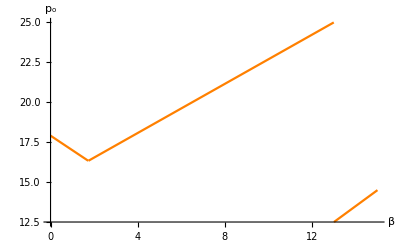

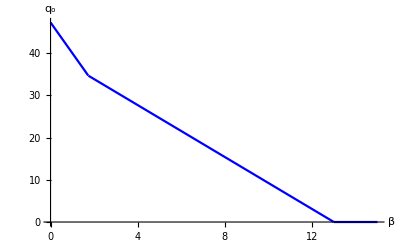

```mathematica
Plot[Piecewise[{{(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))},{(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2),((m+θ) (2 γ θ-λ))/(θ (-2+λ))≤β<(m λ+θ λ)/θ},{β-λ,β>(m λ+θ λ)/θ}}],{β,0,15},PlotStyle->Orange,PlotRange->All,AxesLabel->{β,Subscript[p, o]}]
Plot[Piecewise[{{(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2),β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))},{ (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),((m+θ) (2 γ θ-λ))/(θ (-2+λ))≤β<(m λ+θ λ)/θ},{0,β>(m λ+θ λ)/θ}}],{β,0,15},PlotStyle->Blue,PlotRange->All,AxesLabel->{β,Subscript[q, o]}]
```

## Hybrid Model

## Basic Model

```mathematica
Clear["Global`*"]
d[p_,q_]:=m-θ*p+λ*q
Π[p_,q_]:=(p-c)*q -γ*q^2
Α[p_,q_]:=(p-c)*d[p,q] -α*(q-d[p,q])-γ*q^2
```

```mathematica
Simplify[D[Α[p,q], q]]
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], q],q]]
Simplify[D[D[Α[p,q], p],p]]
Simplify[D[D[Α[p,q], p],q]]
```

-2 q γ+α (-1+λ)+(-c+p) λ

m+c θ-2 p θ-α θ+q λ

-2 γ

-2 θ

λ

### FOC

```mathematica
Simplify[Solve[D[Α[p,q], p]==0 && D[Α[p,q], q]==0,{p,q}]]
```

{{p→(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),q→(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>0&&0<d[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]≤(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]] 
Simplify[Reduce[Α[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
```

θ>0&&0<λ<1&&((4 γ>λ^2/θ&&2 γ<λ^2/θ&&m>0&&((0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α+(m (-2 γ θ+λ))/(θ (-1+λ))==0&&c<m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α>(m (2 γ θ-λ))/(θ (-1+λ))&&c<(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2))))||(2 γ==λ^2/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(2 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2)<c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ)))

α∈ℝ&&m>0&&γ>0&&0<λ<1&&λ^2/γ<4 θ&&λ/γ>2 θ&&(c<m/θ||(c==m/θ&&(α<(c θ (2 γ θ-λ)+m (-2 γ θ+λ)+θ (1+γ θ-λ) √(-((m-c θ)^2 (4 γ θ-λ^2))/(θ^2 (1+γ θ-λ)^2)))/(2 θ (1+γ θ-λ))||α>(c θ (2 γ θ-λ)+m (-2 γ θ+λ)+θ (1+γ θ-λ) √(-((m-c θ)^2 (4 γ θ-λ^2))/(θ^2 (1+γ θ-λ)^2)))/(2 θ (1+γ θ-λ))))||c>m/θ)

```mathematica
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>c&&(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>0&&0<d[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]≤(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)&&Α[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
```

θ>0&&0<λ<1&&((4 γ>λ^2/θ&&2 γ<λ^2/θ&&m>0&&((0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α+(m (-2 γ θ+λ))/(θ (-1+λ))==0&&c<m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α>(m (2 γ θ-λ))/(θ (-1+λ))&&c<(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2))))||(2 γ==λ^2/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(2 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2)<c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ)))

### If FOC not feasible

```mathematica
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>0&&0<d[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]≤(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ,{α,c}]]
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
Simplify[Reduce[0<d[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)]≤(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
```

θ>0&&0<λ<1&&((4 γ>λ^2/θ&&2 γ<λ^2/θ&&m>0&&((0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α+(m (-2 γ θ+λ))/(θ (-1+λ))==0&&c<m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(α>(m (2 γ θ-λ))/(θ (-1+λ))&&c<(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2))))||(2 γ==λ^2/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ))||(2 γ>λ^2/θ&&2 γ<λ/θ&&m>0&&0<α<(m (2 γ θ-λ))/(θ (-1+λ))&&(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2)<c≤m/θ+(2 α (1+γ θ-λ))/(2 γ θ-λ)))

c∈ℝ&&θ>0&&0<λ<1&&m>0&&((2 γ==λ^2/θ&&0<α<(2 m γ)/(2 γ θ+λ-λ^2))||(α>0&&((4 γ>λ^2/θ&&2 γ<λ^2/θ&&c<(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2))||(c>(-2 m γ+α (2 γ θ+λ-λ^2))/(2 γ θ-λ^2)&&2 γ>λ^2/θ&&2 γ<λ/θ))))

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&2 α θ (1+γ θ-λ)+(m-c θ) (2 γ θ-λ)≤0

```mathematica
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[D[D[Α[p,(α (-1+λ)+(-c+p) λ)/(2 γ)], p],p]]
Simplify[Solve[D[Α[p,(α (-1+λ)+(-c+p) λ)/(2 γ)], p]==0,p]]
```

{{q→(α (-1+λ)+(-c+p) λ)/(2 γ)}}

-2 θ+λ^2/(2 γ)

{{p→(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[0<d[p,(α (-1+λ)+(-c+p) λ)/(2 γ)]≤(α (-1+λ)+(-c+p) λ)/(2 γ)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ,p]]
Simplify[Reduce[d[p,(α (-1+λ)+(-c+p) λ)/(2 γ)]≤(α (-1+λ)+(-c+p) λ)/(2 γ)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ,p]]
Simplify[Reduce[d[p,(α (-1+λ)+(-c+p) λ)/(2 γ)]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ,p]]
Simplify[Reduce[(α (-1+λ)+(-c+p) λ)/(2 γ)>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ,p]]
```

θ>0&&0<λ<1&&((4 γ>λ^2/θ&&2 γ<λ^2/θ&&α>0&&m>0&&((c+α/λ<α+m/θ&&p≥(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2))||(c+α/λ==α+m/θ&&p>(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2))||(c+α/λ>α+m/θ&&p>(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2))))||(2 γ==λ^2/θ&&α>0&&m>0&&c+α/λ<α+m/θ&&p≥(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2))||(2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ&&(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)≤p<(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2)))

c∈ℝ&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&p≥(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)

(c|p)∈ℝ&&θ>0&&0<λ<1&&m>0&&α>0&&((2 γ==λ^2/θ&&c<(2 m γ+α (-1+λ) λ)/λ^2)||(p>(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2)&&4 γ>λ^2/θ&&2 γ<λ^2/θ)||(2 γ>λ^2/θ&&2 γ<λ/θ&&p<(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2)))

c∈ℝ&&m>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&c+α/λ<p+α

#### Case 1

```mathematica
Simplify[(α (-1+λ)+(-c+(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)) λ)/(2 γ)]
Simplify[d[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]-(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]
```

(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)

0

```mathematica
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]≤0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ^2/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
```

False

#### Case 2

```mathematica
Simplify[(α (-1+λ)+(-c+(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2)) λ)/(2 γ)]
Simplify[d[(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ-λ^2)]]
```

(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ-λ^2)

0

#### Case 3

```mathematica
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)<(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)&&θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
Simplify[Reduce[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)>(2 m γ+λ (α (-1+λ)-c λ))/(2 γ θ-λ^2)&&θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
```

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<2 γ θ&&2 γ θ<λ&&2 α θ (1+γ θ-λ)+(m-c θ) (2 γ θ-λ)>0&&θ (α+c λ)<(m+α θ) λ

False

```mathematica
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]≤0&&θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
```

False

```mathematica
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]>Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
Simplify[Reduce[Α[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)]<Π[(c+2 m γ-c λ)/(1+2 γ θ-λ),(m-c θ)/(1+2 γ θ-λ)]&&θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c+α/λ<α+m/θ]]
```

θ>0&&0<λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&c<m/θ+(α (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))/(2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ)

θ>0&&0<λ&&λ<1&&2 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0&&m/θ+(α (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))/(2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ)<c&&c+α/λ<α+m/θ

## Comparative Stats

### Interior

```mathematica
(* Interior soln *)
Simplify[D[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),α]]
Simplify[D[(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2),α]]
Simplify[D[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),c]]
Simplify[D[(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2),c]]
```

(-2 γ θ+(-1+λ) λ)/(4 γ θ-λ^2)

(θ (-2+λ))/(4 γ θ-λ^2)

(2 γ θ-λ^2)/(4 γ θ-λ^2)

-(θ λ)/(4 γ θ-λ^2)

```mathematica
Simplify[Reduce[D[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2),c]<0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
```

False

False

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<2 γ θ&&2 γ θ<λ

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ^2

False

### B2

```mathematica
(* Boundary soln *)
Simplify[D[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),α]]
Simplify[D[(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2),α]]
Simplify[D[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),c]]
Simplify[D[(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2),c]]
```

(-1+λ)^2/(2 γ θ+λ-λ^2)

(θ (-1+λ))/(2 γ θ+λ-λ^2)

((-1+λ) λ)/(-2 γ θ+(-1+λ) λ)

-(θ λ)/(2 γ θ+λ-λ^2)

```mathematica
Simplify[Reduce[D[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2),α]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
Simplify[Reduce[D[(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&α>0&&m>0]]
```

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

False

θ>0&&λ>0&&α>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

False

### B1

```mathematica
(* Bound 1 *)
Simplify[D[(c+2 m γ-c λ)/(1+2 γ θ-λ),α]]
Simplify[D[(m-c θ)/(1+2 γ θ-λ),α]]
Simplify[D[(c+2 m γ-c λ)/(1+2 γ θ-λ),c]]
Simplify[D[(m-c θ)/(1+2 γ θ-λ),c]]
```

0

0

(-1+λ)/(-1-2 γ θ+λ)

-θ/(1+2 γ θ-λ)

```mathematica
Simplify[Reduce[D[(c+2 m γ-c λ)/(1+2 γ θ-λ),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
Simplify[Reduce[D[(c+2 m γ-c λ)/(1+2 γ θ-λ),c]<0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
Simplify[Reduce[D[(m-c θ)/(1+2 γ θ-λ),c]>0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
Simplify[Reduce[D[(m-c θ)/(1+2 γ θ-λ),c]<0&&θ>0&&0<λ<1&&4 γ>λ^2/θ&&2 γ<λ/θ&&m>0]]
```

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

False

False

θ>0&&λ>0&&m>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ

## Coordination

### β≤((m+θ) (2 γ θ-λ))/(θ (-2+λ))

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)==(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)&&(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)==(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2),{α,c}]]
```

{{α→β,c→-1+β}}

```mathematica
(* Check *)
X[p_,q_]:=(p+1-β)*d[p,q] -β*(q-d[p,q])-γ*q^2
Simplify[Solve[D[X[p,q], p]==0 && D[X[p,q], q]==0,{p,q}]]
```

{{p→(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),q→(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)}}

```mathematica
Simplify[Reduce[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2)>0&&0<d[(2 m γ-2 γ θ-β λ+λ^2)/(4 γ θ-λ^2),(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)]≤(-2 β θ+(m+θ) λ)/(4 γ θ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]]
```

α>0&&θ>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((0<m<θ&&((λ>0&&m/θ+λ≤1&&β<(2 m γ-2 γ θ+λ^2)/λ)||(m/θ+λ>1&&λ<1&&β≤((m+θ) (2 γ θ-λ))/(θ (-2+λ)))))||(m≥θ&&0<λ<1&&β≤((m+θ) (2 γ θ-λ))/(θ (-2+λ))))

### β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),{α,c}]]
Simplify[Solve[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),c]]
Simplify[Solve[(c+2 m γ-c λ)/(1+2 γ θ-λ)==(β+2 m γ-λ-β λ+λ^2)/(2 γ θ+λ-λ^2)&&(m-c θ)/(1+2 γ θ-λ)== (-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2),c]]
```

{{α→-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),c→(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2))}}

{{c→(β+α (-1+λ)-λ)/λ}}

{{c→(β (1+2 γ θ-λ)-2 m γ (-1+λ)+λ (-1-2 γ θ+λ))/(2 γ θ+λ-λ^2)}}

```mathematica
(* Check *)
X[p_,q_]:=(p-(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)))*d[p,q] +((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2))*(q-d[p,q])-γ*q^2
Simplify[Solve[D[X[p,q], p]==0 && D[X[p,q], q]==0,{p,q}]]
```

{{p→(β+2 m γ-β λ+(-1+λ) λ)/(2 γ θ+λ-λ^2),q→(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)}}

```mathematica
Simplify[Reduce[(β+2 m γ-β λ+(-1+λ) λ)/(2 γ θ+λ-λ^2)>0&&0<d[(β+2 m γ-β λ+(-1+λ) λ)/(2 γ θ+λ-λ^2),(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)]≤(-β θ+(m+θ) λ)/(2 γ θ+λ-λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&m+θ λ>θ]]
```

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

```mathematica
Reduce[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2))>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]
Simplify[(-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)) (2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))/(2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ)]
Reduce[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2))<m/θ+-((2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) (2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ) (2 γ θ+λ-λ^2))&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ]
```

θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>0&&β<(m λ+θ λ)/θ

-((2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) (2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ) (2 γ θ+λ-λ^2))

θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>0&&β<(m λ+θ λ)/θ

### β>(m λ+θ λ)/θ

```mathematica
Simplify[Solve[(2 m γ+2 c γ θ-2 α γ θ-α λ-c λ^2+α λ^2)/(4 γ θ-λ^2)==β-λ&&(α θ (-2+λ)+(m-c θ) λ)/(4 γ θ-λ^2)== 0,{α,c}]]
Simplify[Solve[(2 m γ+α (-1+λ)^2-c (-1+λ) λ)/(2 γ θ+λ-λ^2)==β-λ&&(α θ (-1+λ)+(m-c θ) λ)/(2 γ θ+λ-λ^2)== 0,c]]
Simplify[Solve[(c+2 m γ-c λ)/(1+2 γ θ-λ)==β-λ&&(m-c θ)/(1+2 γ θ-λ)== 0,c]]
```

{{α→(λ (m+θ (-β+λ)))/θ,c→-(β-λ) (-2+λ)+(m (-1+λ))/θ}}

{}

{}

```mathematica
Simplify[((λ (m+θ (-β+λ)))/θ(2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2))/(2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ)]
```

((2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ (m+θ (-β+λ)))/(θ (2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ))

```mathematica
Simplify[Reduce[(λ (m+θ (-β+λ)))/θ>0&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[-(β-λ) (-2+λ)+(m (-1+λ))/θ<m/θ+((2 γ^2 θ^2-3 γ θ (-1+λ)+(-1+λ)^2) λ (m+θ (-β+λ)))/(θ (2 γ^2 θ^2-2 γ θ λ+(-1+λ) λ))&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ]]
```

θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

```mathematica
X[p_,q_]:=(p-(-(β-λ) (-2+λ)+(m (-1+λ))/θ))*d[p,q] +(λ (m+θ (-β+λ)))/θ*(q-d[p,q])-γ*q^2
Simplify[Solve[D[X[p,q], p]==0 && D[X[p,q], q]==0,{p,q}]]
```

{{p→(β θ (-4 γ θ (-1+λ)+λ^2 (-3+2 λ))+λ (2 m (2 γ θ+λ-λ^2)+θ (4 γ θ (-1+λ)+(3-2 λ) λ^2)))/(θ (4 γ θ-λ^2)),q→(2 (-2+λ) λ (m+θ (-β+λ)))/(-4 γ θ+λ^2)}}

```mathematica
Simplify[Reduce[(β θ (-4 γ θ (-1+λ)+λ^2 (-3+2 λ))+λ (2 m (2 γ θ+λ-λ^2)+θ (4 γ θ (-1+λ)+(3-2 λ) λ^2)))/(θ (4 γ θ-λ^2))>0&&0<d[(β θ (-4 γ θ (-1+λ)+λ^2 (-3+2 λ))+λ (2 m (2 γ θ+λ-λ^2)+θ (4 γ θ (-1+λ)+(3-2 λ) λ^2)))/(θ (4 γ θ-λ^2)),(2 (-2+λ) λ (m+θ (-β+λ)))/(-4 γ θ+λ^2)]≤(2 (-2+λ) λ (m+θ (-β+λ)))/(-4 γ θ+λ^2)&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ]]
```

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

### Comparative Stats

#### w.r.t β

```mathematica
Clear["Global`*"]
```

```mathematica
Simplify[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),β]]
Simplify[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),β]]
```

(2 γ θ-λ)/(2 γ θ+λ-λ^2)

(2+2 γ θ-2 λ)/(2 γ θ+λ-λ^2)

```mathematica
Reduce[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),β]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&m+θ λ>θ]
Reduce[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),β]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&m+θ λ>θ]
```

α>0&&θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>θ-θ λ&&β>(2 m γ θ+2 γ θ^2-m λ-θ λ)/(-2 θ+θ λ)

α>0&&θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>θ-θ λ&&β>(2 m γ θ+2 γ θ^2-m λ-θ λ)/(-2 θ+θ λ)

```mathematica
Simplify[D[(λ (m+θ (-β+λ)))/θ,β]]
Simplify[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,β]]
```

-λ

2-λ

```mathematica
Reduce[D[(λ (m+θ (-β+λ)))/θ,β]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ]
Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,β]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ]
```

α>0&&θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>θ-θ λ&&β>(m λ+θ λ)/θ

α>0&&θ>0&&0<λ<1&&λ^2/(4 θ)<γ<λ/(2 θ)&&m>θ-θ λ&&β>(m λ+θ λ)/θ

#### w.r.t. λ

```mathematica
Clear["Global`*"]
```

```mathematica
Simplify[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),λ]]
Simplify[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),λ]]
```

(β θ (4 γ θ (-1+λ)-λ^2)-(m+θ) (4 γ^2 θ^2+2 γ θ (-2+λ) λ-λ^2))/(θ (2 γ θ+λ-λ^2)^2)

-(2 (β (γ θ (3-2 λ)+(-1+λ)^2)+γ (m+θ) (2+2 γ θ-4 λ+λ^2)))/((2 γ θ+λ-λ^2)^2)

```mathematica
Simplify[Reduce[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),λ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),λ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),λ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),λ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
```

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

False

False

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

```mathematica
Simplify[D[(λ (m+θ (-β+λ)))/θ,λ]]
Simplify[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,λ]]
```

-β+m/θ+2 λ

-2-β+m/θ+2 λ

```mathematica
Simplify[Reduce[D[(λ (m+θ (-β+λ)))/θ,λ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[(λ (m+θ (-β+λ)))/θ,λ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,λ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,λ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
```

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

False

α>0&&θ>0&&m>0&&λ>0&&2 θ<m&&m (-1+λ)<θ (-2+λ)&&(m+θ) λ<β θ&&θ (2+β-2 λ)<m&&λ^2<4 γ θ&&2 γ θ<λ

α>0&&θ>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((λ+(m λ)/θ<β<m/θ+λ&&λ<1&&((m/θ+λ>1&&0<m&&m≤θ)||(0<λ&&θ<m&&m≤2 θ)||(m>2 θ&&(m-2 θ)/(m-θ)<λ)))||(0<λ≤(m-2 θ)/(m-θ)&&-2+m/θ+2 λ<β<m/θ+λ&&m>2 θ))

```mathematica
Simplify[Solve[-2-β+m/θ+2 λ==0,λ]]
```

{{λ→1/2 (2+β-m/θ)}}

```mathematica
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,λ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ&&m>0&&m>θ]]
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,λ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&m+θ λ>θ&&m>0&&m>θ]]
```

α>0&&θ>0&&m>0&&λ>0&&2 θ<m&&m (-1+λ)<θ (-2+λ)&&λ^2<4 γ θ&&2 γ θ<λ&&(m+θ) λ<β θ&&θ (2+β-2 λ)<m

α>0&&θ>0&&4 γ>λ^2/θ&&2 γ<λ/θ&&((β>λ+(m λ)/θ&&λ<1&&((0<λ&&θ<m&&m≤2 θ)||(m>2 θ&&(m-2 θ)/(m-θ)<λ)))||(0<λ≤(m-2 θ)/(m-θ)&&m>2 θ&&β>-2+m/θ+2 λ))

#### w.r.t. θ

```mathematica
Clear["Global`*"]
```

```mathematica
Simplify[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),θ]]
Simplify[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),θ]]
```

(λ (-2 β γ θ^2 (-2+λ)+2 γ θ^2 (-2+λ) λ+m (4 γ^2 θ^2-4 γ θ λ+(-1+λ) λ^2)))/(θ^2 (2 γ θ+λ-λ^2)^2)

((-1+λ) (-2 β γ θ^2 (-2+λ)+2 γ θ^2 (-2+λ) λ+m (4 γ^2 θ^2-4 γ θ λ+(-1+λ) λ^2)))/(θ^2 (2 γ θ+λ-λ^2)^2)

```mathematica
Simplify[Reduce[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),θ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),θ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),θ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
Simplify[Reduce[D[(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),θ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>((m+θ) (2 γ θ-λ))/(θ (-2+λ))&&β<(m λ+θ λ)/θ&&m+θ λ>θ]]
```

False

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&λ<2&&(m+θ+β θ) λ<2 θ (β+γ (m+θ))&&β θ<(m+θ) λ

False

```mathematica
Simplify[D[(λ (m+θ (-β+λ)))/θ,θ]]
Simplify[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,θ]]
```

-(m λ)/θ^2

(m-m λ)/θ^2

```mathematica
Simplify[Reduce[D[(λ (m+θ (-β+λ)))/θ,θ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[(λ (m+θ (-β+λ)))/θ,θ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,θ]>0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
Simplify[Reduce[D[-(β-λ) (-2+λ)+(m (-1+λ))/θ,θ]<0&&0<α&&0<γ&&θ>0&&m>0&&0<λ<1&&4γ>λ^2/θ&&2 γ<λ/θ&&β>(m λ+θ λ)/θ&&β<m/θ+λ&&m+θ λ>θ]]
```

False

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

α>0&&θ>0&&λ>0&&λ<1&&λ^2<4 γ θ&&2 γ θ<λ&&θ<m+θ λ&&(m+θ) λ<β θ&&β θ<m+θ λ

False

### Plots

```mathematica
m = 50;λ = 0.5; θ = 2; γ = 0.1;
(m λ+θ λ)/θ
```

13.

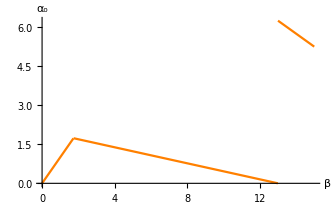

```mathematica
Plot[Piecewise[{{β,β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))},{-((2 γ θ-λ) (-β θ+(m+θ) λ))/(θ (2 γ θ+λ-λ^2)),((m+θ) (2 γ θ-λ))/(θ (-2+λ))≤β<(m λ+θ λ)/θ},{(λ (m+θ (-β+λ)))/θ,β>(m λ+θ λ)/θ}}],{β,0,15},PlotStyle->Orange,PlotRange->All,AxesLabel->{β,Subscript[α, o]}]
```

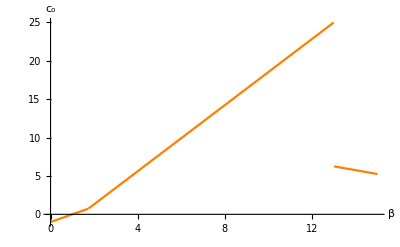

```mathematica
Plot[Piecewise[{{-1+β,β<((m+θ) (2 γ θ-λ))/(θ (-2+λ))},{(2 β θ (1+γ θ-λ)-m (2 γ θ-λ) (-1+λ)+2 θ λ (-1-γ θ+λ))/(θ (2 γ θ+λ-λ^2)),-(β-λ) (-2+λ)+(m (-1+λ))/θ≤β<(m λ+θ λ)/θ},{(λ (m+θ (-β+λ)))/θ,β>(m λ+θ λ)/θ}}],{β,0,15},PlotStyle->Orange,PlotRange->All,AxesLabel->{β,Subscript[c, o]}]
```